# Eulerian Graph Q function

## Undirected graphs

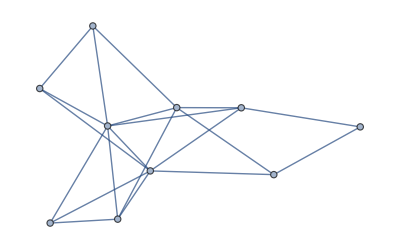

```mathematica
RandomGraph[{10,20}]
```

```mathematica
EulerianGraphQ[RandomGraph[{10,20}]]
```

False

## Directed Graphs

```mathematica
RandomGraph[{10,20},DirectedEdges->True]
```

-Graphics-

```mathematica
EulerianGraphQ[RandomGraph[{10,20},DirectedEdges->True]]
```

False

## Mixed Graphs

### Even

```mathematica
EvenCondition[graph_?ConnectedGraphQ]:=AllTrue[VertexDegree[graph],EvenQ]
```

```mathematica
Needs["PeterBurbery`MixedGraphs`"]
```

Get::noopen: Cannot open PeterBurbery`MixedGraphs`.

Needs::nocont: Context PeterBurbery`MixedGraphs` was not created when Needs was evaluated.

$Failed

```mathematica
PacletInstall[ResourceObject["PeterBurbery/MixedGraphs"]]
```

PacletObject[…]

## Even but not balanced

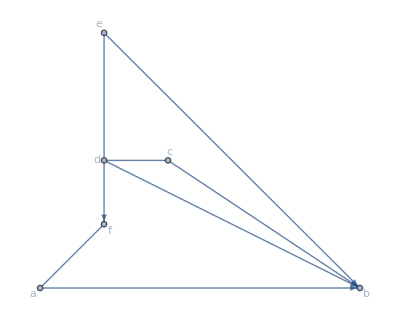

```mathematica
evenbutnotbalanced=Graph[{a->b,b<->c,c<->d,d->b,d<->e,d->f,f<->a,e->b},VertexLabels->Automatic,GraphLayout->"PlanarEmbedding"]
```

```mathematica
EulerianGraphQ[evenbutnotbalanced]
```

EulerianGraphQ::ngen: The generalized EulerianGraphQ[Graph[<6>, <8>]] is not implemented.

EulerianGraphQ[-Graphics-]

```mathematica
EvenCondition[evenbutnotbalanced]
```

True

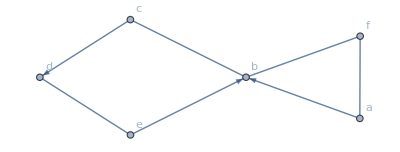

```mathematica
evenandbalanced=Graph[{a,b,c,d,e,f},{a->b,b<->c,c->d,d<->e,e->b,a<->f,f<->b},VertexLabels->Automatic]
```

```mathematica
EvenCondition[evenandbalanced]
```

True

## Balanced Set Condition

```mathematica
VertexList[evenandbalanced]
```

{a,b,c,d,e,f}

```mathematica
Subsets[VertexList[evenandbalanced]]
```

{{},{a},{b},{c},{d},{e},{f},{a,b},{a,c},{a,d},{a,e},{a,f},{b,c},{b,d},{b,e},{b,f},{c,d},{c,e},{c,f},{d,e},{d,f},{e,f},{a,b,c},{a,b,d},{a,b,e},{a,b,f},{a,c,d},{a,c,e},{a,c,f},{a,d,e},{a,d,f},{a,e,f},{b,c,d},{b,c,e},{b,c,f},{b,d,e},{b,d,f},{b,e,f},{c,d,e},{c,d,f},{c,e,f},{d,e,f},{a,b,c,d},{a,b,c,e},{a,b,c,f},{a,b,d,e},{a,b,d,f},{a,b,e,f},{a,c,d,e},{a,c,d,f},{a,c,e,f},{a,d,e,f},{b,c,d,e},{b,c,d,f},{b,c,e,f},{b,d,e,f},{c,d,e,f},{a,b,c,d,e},{a,b,c,d,f},{a,b,c,e,f},{a,b,d,e,f},{a,c,d,e,f},{b,c,d,e,f},{a,b,c,d,e,f}}

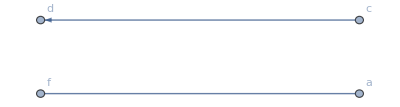

```mathematica
Subgraph[evenandbalanced,{a,c,d,f}]
```

```mathematica
evenandbalanced
```

-Graphics-

## New Work

```mathematica
EdgeCount[evenandbalanced,Alternatives@@{a,c,d,f}->_]
```

2

```mathematica
EdgeCount[evenandbalanced,_->Alternatives@@{a,c,d,f}]
```

1

```mathematica
EdgeCount[evenandbalanced,_<->Alternatives@@{a,c,d,f}]
```

4

```mathematica
EdgeList[evenandbalanced,_<->Alternatives@@{a,c,d,f}]
```

{b<->c,d<->e,a<->f,f<->b}

```mathematica
EdgeCount[evenandbalanced,Alternatives@@{a,c,d,f}<->_]
```

4

```mathematica
EdgeCount[evenandbalanced,Alternatives@@{a,c,d,f}<->_]
```

```mathematica
EdgeList[evenandbalanced,Alternatives@@{a,c,d,f}<->_]
```

{b<->c,d<->e,a<->f,f<->b}

```mathematica
VertexDegree[evenandbalanced,#]&/@{a,c,d,f}
```

{2,2,2,2}

```mathematica
EdgeCount[evenandbalanced,Alternatives@@{a,c,d,f}->_]-EdgeCount[evenandbalanced,_->Alternatives@@{a,c,d,f}]
```

1

```mathematica
EdgeCount[evenandbalanced,Alternatives@@{a,c,d,f}->_]-EdgeCount[evenandbalanced,_->Alternatives@@{a,c,d,f}]<=EdgeCount[evenandbalanced,_<->Alternatives@@{a,c,d,f}]
```

True

```mathematica
AllTrue[Subsets[VertexList[evenandbalanced]],EdgeCount[evenandbalanced,Alternatives@@#->_]-EdgeCount[evenandbalanced,_->Alternatives@@#]<=EdgeCount[evenandbalanced,_<->Alternatives@@#]&]
```

True

```mathematica
AllTrue[Subsets[VertexList[evenbutnotbalanced]],EdgeCount[evenbutnotbalanced,Alternatives@@#->_]-EdgeCount[evenbutnotbalanced,_->Alternatives@@#]<=EdgeCount[evenbutnotbalanced,_<->Alternatives@@#]&]
```

False

```mathematica
MixedEulerianGraphQ[graph_?ConnectedGraphQ]:=AllTrue[Subsets[VertexList[graph]],EdgeCount[graph,Alternatives@@#->_]-EdgeCount[graph,_->Alternatives@@#]<=EdgeCount[graph,_<->Alternatives@@#]&]
```

```mathematica
MixedEulerianGraphQ[evenbutnotbalanced]
```

False

```mathematica
MixedEulerianGraphQ[evenandbalanced]
```

True

## Test case

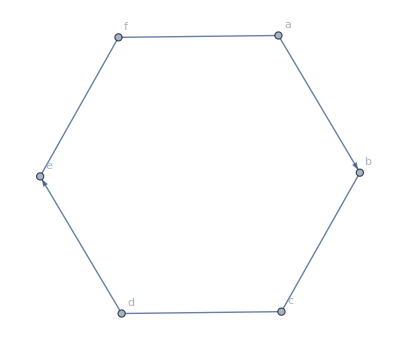

```mathematica
Graph[{a,b,c,d,e,f},{a->b,b<->c,c<->d,d->e,e<->f,a<->f},VertexLabels->Automatic,ImageSize->Full]
```

```mathematica
MixedEulerianGraphQ[Graph[{a,b,c,d,e,f},{a->b,b<->c,c<->d,d->e,e<->f,a<->f},VertexLabels->Automatic,ImageSize->Full]]
```

True

## Previous Work

```mathematica
IncidenceList[evenandbalanced,Alternatives@@{a,c,d,f}]
```

{a->b,b<->c,c->d,d<->e,a<->f,f<->b}

```mathematica
EdgeCount[evenandbalanced,_->Alternatives@@{a,c,d,f}]
```

1

```mathematica
EdgeCount[evenandbalanced,Alternatives@@{a,c,d,f}->_]
```

2

```mathematica
AllTrue[Subsets[VertexList[evenandbalanced]],EdgeCount[evenandbalanced,_->Alternatives@@#]<=EdgeCount[evenandbalanced,Alternatives@@#->_]&]
```

False

```mathematica
?AllTrue
```

```mathematica
AllTrue[Subsets[VertexList[evenandbalanced]],EdgeCount[evenandbalanced,_->Alternatives@@#]>=EdgeCount[evenandbalanced,Alternatives@@#->_]&]
```

False

```mathematica
Select[!(EdgeCount[evenandbalanced,_->Alternatives@@#]<=EdgeCount[evenandbalanced,Alternatives@@#->_])&][Subsets[VertexList[evenandbalanced]]]
```

{{b},{d},{a,b},{b,c},{b,d},{b,e},{b,f},{d,f},{a,b,d},{a,b,f},{b,c,d},{b,c,f},{b,d,e},{b,d,f},{b,e,f},{a,b,c,d},{a,b,d,e},{a,b,d,f},{b,c,d,e},{b,c,d,f},{b,d,e,f},{a,b,c,d,f},{a,b,d,e,f},{b,c,d,e,f}}

```mathematica
EdgeCount[evenandbalanced,_->Alternatives@@#]<=EdgeCount[evenandbalanced,Alternatives@@#->_]&[{b,f}]
```

False

```mathematica
EdgeList[evenandbalanced,_->b|f]
```

{a->b,e->b}

```mathematica
EdgeList[evenandbalanced,b|f->_]
```

{}

```mathematica
AllTrue[Subsets[VertexList[evenbutnotbalanced]],EdgeCount[evenbutnotbalanced,_->Alternatives@@#]<=EdgeCount[evenbutnotbalanced,Alternatives@@#->_]&]
```

False

```mathematica
Table[{EdgeCount[evenbutnotbalanced,_->Alternatives@@k],EdgeCount[evenbutnotbalanced,Alternatives@@#->_]&[k],EdgeCount[evenbutnotbalanced,Alternatives@@k<->_]},{k,Subsets[VertexList[evenbutnotbalanced]]}]
```

{{0,0,0},{0,1,1},{3,0,1},{0,0,2},{0,2,2},{0,1,1},{1,0,1},{3,1,2},{0,1,3},{0,3,3},{0,2,2},{1,1,1},{3,0,2},{3,2,3},{3,1,2},{4,0,2},{0,2,3},{0,1,3},{1,0,3},{0,3,2},{1,2,3},{1,1,2},{3,1,3},{3,3,4},{3,2,3},{4,1,2},{0,3,4},{0,2,4},{1,1,3},{0,4,3},{1,3,3},{1,2,2},{3,2,3},{3,1,3},{4,0,3},{3,3,3},{4,2,4},{4,1,3},{0,3,3},{1,2,4},{1,1,4},{1,3,3},{3,3,4},{3,2,4},{4,1,3},{3,4,4},{4,3,4},{4,2,3},{0,4,4},{1,3,4},{1,2,4},{1,4,3},{3,3,3},{4,2,4},{4,1,4},{4,3,4},{1,3,4},{3,4,4},{4,3,4},{4,2,4},{4,4,4},{1,4,4},{4,3,4},{4,4,4}}

## Eulerize Graph

```mathematica
Names["*Closure*",IgnoreCase->True]
```

{TransitiveClosureGraph}

```mathematica
Names["*match*",IgnoreCase->True]
```

{AutoMatch,ConfirmMatch,DayMatchQ,DelimiterAutoMatching,DelimiterMatching,FindMatchingColor,LongestMatch,MatchingDissimilarity,MatchLocalNameQ,MatchLocalNames,MatchQ,MoleculeMatchQ,ShortestMatch,SpeakerMatchQ,StringMatchQ}

```mathematica
Information/@Names["*match*",IgnoreCase->True]
```

{,,,,,,,,,,,,,,}

```mathematica
Names["*edge*",IgnoreCase->True]
```

{AxesEdge,DirectedEdge,DirectedEdges,DrawEdges,EdgeAdd,EdgeBetweennessCentrality,EdgeCapacity,EdgeCapForm,EdgeChromaticNumber,EdgeColor,EdgeConnectivity,EdgeContract,EdgeCost,EdgeCount,EdgeCoverQ,EdgeCycleMatrix,EdgeDashing,EdgeDelete,EdgeDetect,EdgeForm,EdgeIndex,EdgeJoinForm,EdgeLabeling,EdgeLabels,EdgeLabelStyle,EdgeList,EdgeOpacity,EdgeQ,EdgeRenderingFunction,EdgeRules,EdgeShapeFunction,EdgeStyle,EdgeTaggedGraph,EdgeTaggedGraphQ,EdgeTags,EdgeThickness,EdgeTransitiveGraphQ,EdgeValueRange,EdgeValueSizes,EdgeWeight,EdgeWeightedGraphQ,FindEdgeColoring,FindEdgeCover,FindEdgeCut,FindEdgeIndependentPaths,FindIndependentEdgeSet,IndependentEdgeSetQ,IndexEdgeTaggedGraph,KEdgeConnectedComponents,KEdgeConnectedGraphQ,MultiedgeStyle,ParentEdgeLabel,ParentEdgeLabelFunction,ParentEdgeLabelStyle,ParentEdgeShapeFunction,ParentEdgeStyle,ParentEdgeStyleFunction,TensorWedge,UndirectedEdge,Wedge}

```mathematica
Information/@Names["*edge*",IgnoreCase->True]
```

{,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,}

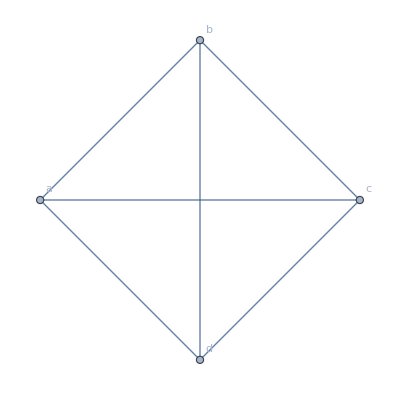

```mathematica
Graph[{a,b,c,d},{a<->b,a<->c,a<->d,b<->c,b<->d,c<->d},VertexLabels->Automatic,EdgeWeight->{2,3,5,7,11,13}]
```

```mathematica
Iconize[Graph[{a,b,c,d},{a<->b,a<->c,a<->d,b<->c,b<->d,c<->d},VertexLabels->Automatic,EdgeWeight->{2,3,5,7,11,13}],"Graph"]
```

```mathematica
FindEdgeCover[]
```

{a<->b,a<->c,a<->d}

```mathematica
FindVertexCover[]
```

{a,b,c}

```mathematica
FindIndependentEdgeSet[]
```

{a<->b,c<->d}

```mathematica
FindIndependentVertexSet[]
```

{{a}}

```mathematica
FindClique[]
```

{{a,b,c,d}}

```mathematica
Iconize[Graph[{a,b,c,d},{a<->b,a<->c,a<->d,b<->c,b<->d,c<->d},VertexLabels->Automatic,EdgeWeight->-{2,3,5,7,11,13}],"Graph"]
```

```mathematica
FindEdgeCover[]
```

FindEdgeCover[-Graphics-]

```mathematica
FindIndependentEdgeSet[]
```

{a<->d,b<->c}

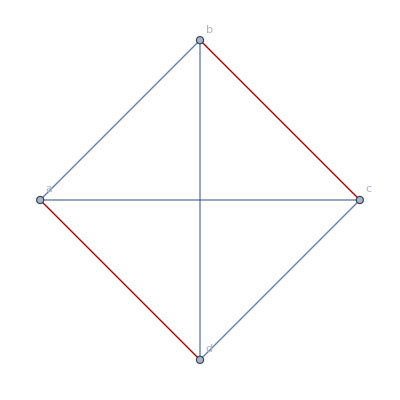

```mathematica
HighlightGraph[Graph[{a, b, c, d}, {UndirectedEdge[a, b], UndirectedEdge[a, c], UndirectedEdge[a, d], UndirectedEdge[b, c], UndirectedEdge[b, d], UndirectedEdge[c, d]}, {VertexLabels -> {Automatic}, EdgeWeight -> {-2, -3, -5, -7, -11, -13}}],{a<->d,b<->c}]
```

```mathematica
Subsets[{a,b,c,d,e,f},{2}]
```

{{a,b},{a,c},{a,d},{a,e},{a,f},{b,c},{b,d},{b,e},{b,f},{c,d},{c,e},{c,f},{d,e},{d,f},{e,f}}

```mathematica
Length[Subsets[{a,b,c,d,e,f},{2}]]
```

15

```mathematica
Binomial[6,2]
```

15

```mathematica
UndirectedEdge@@@Subsets[{a,b,c,d,e,f},{2}]
```

{a<->b,a<->c,a<->d,a<->e,a<->f,b<->c,b<->d,b<->e,b<->f,c<->d,c<->e,c<->f,d<->e,d<->f,e<->f}

```mathematica
Thread[UndirectedEdge@@@Subsets[{a,b,c,d,e,f},{2}]->Prime[Range[Binomial[6,2]]]]
```

{a<->b→2,a<->c→3,a<->d→5,a<->e→7,a<->f→11,b<->c→13,b<->d→17,b<->e→19,b<->f→23,c<->d→29,c<->e→31,c<->f→37,d<->e→41,d<->f→43,e<->f→47}

```mathematica
Thread[UndirectedEdge@@@Subsets[{a,b,c,d,e,f},{2}]->-Prime[Range[Binomial[6,2]]]]
```

{a<->b→-2,a<->c→-3,a<->d→-5,a<->e→-7,a<->f→-11,b<->c→-13,b<->d→-17,b<->e→-19,b<->f→-23,c<->d→-29,c<->e→-31,c<->f→-37,d<->e→-41,d<->f→-43,e<->f→-47}

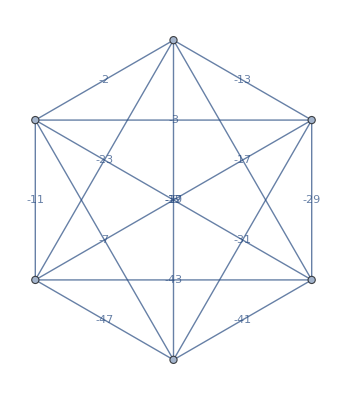

```mathematica
Graph[UndirectedEdge@@@Subsets[{a,b,c,d,e,f},{2}],EdgeWeight->Thread[UndirectedEdge@@@Subsets[{a,b,c,d,e,f},{2}]->-Prime[Range[Binomial[6,2]]]],EdgeLabels->"EdgeWeight"]
```

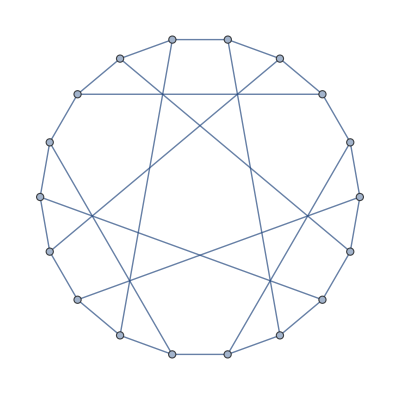

```mathematica
GraphData["PappusGraph"]
```

```mathematica
VertexDegree[GraphData["PappusGraph"]]
```

{3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}

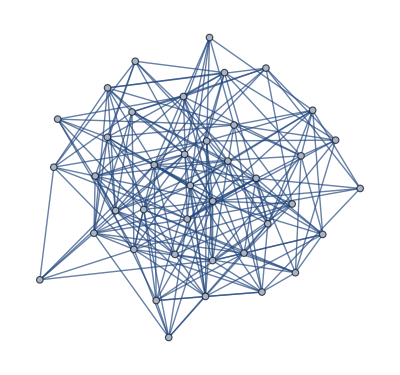

```mathematica
RandomGraph[BernoulliGraphDistribution[40,0.3]]
```

```mathematica
VertexDegree[RandomGraph[BernoulliGraphDistribution[40,0.3]]]
```

{10,11,10,11,16,12,11,13,8,13,14,11,18,15,9,15,16,11,9,8,13,13,8,7,9,15,11,10,10,17,10,17,7,14,16,8,12,14,8,10}

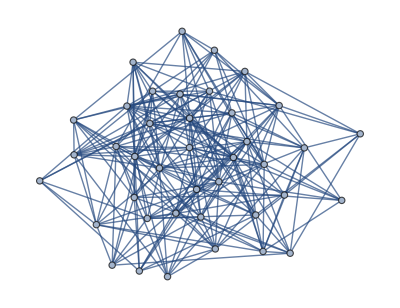

```mathematica
graph=RandomGraph[BernoulliGraphDistribution[40,0.3]]
```

```mathematica
VertexDegree[graph]
```

{8,9,13,12,9,9,10,14,11,12,7,8,9,14,11,10,11,16,17,11,12,16,12,11,9,12,12,15,6,14,11,12,17,14,12,13,11,7,8,15}

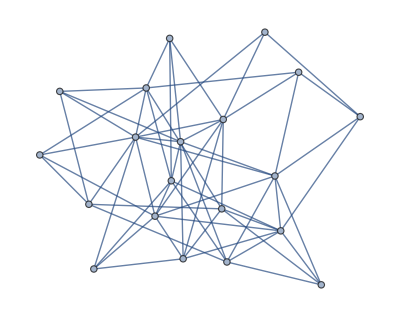

```mathematica
Subgraph[graph,v_/;OddQ[VertexDegree[graph,v]]]
```

```mathematica
VertexDegree[Subgraph[graph,v_/;OddQ[VertexDegree[graph,v]]]]
```

{3,7,4,6,6,5,4,6,10,8,4,7,4,8,4,8,8,4,4,8}

```mathematica
FindSubgraphIsomorphism[Subgraph[graph,v_/;OddQ[VertexDegree[graph,v]]],graph]
```

{<|2→2,3→3,5→5,6→6,9→9,11→11,13→13,15→15,17→17,19→19,20→20,24→24,25→25,28→28,31→31,33→33,36→36,37→18,38→26,40→40|>}

```mathematica
First[FindSubgraphIsomorphism[Subgraph[graph,v_/;OddQ[VertexDegree[graph,v]]],graph]]
```

<|2→2,3→3,5→5,6→6,9→9,11→11,13→13,15→15,17→17,19→19,20→20,24→24,25→25,28→28,31→31,33→33,36→36,37→18,38→26,40→40|>

```mathematica
Normal[<|2->2,3->3,5->5,6->6,9->9,11->11,13->13,15->15,17->17,19->19,20->20,24->24,25->25,28->28,31->31,33->33,36->36,37->18,38->26,40->40|>]
```

{2→2,3→3,5→5,6→6,9→9,11→11,13→13,15→15,17→17,19→19,20→20,24→24,25→25,28→28,31→31,33→33,36→36,37→18,38→26,40→40}

```mathematica
List@@(2->2)
```

{2,2}

```mathematica
Union[List[#]]&@@(2->2)
```

{2}

```mathematica
Union[List[#]]&@@@{2->2}
```

{{2}}

```mathematica
Union[List[#]]&@@@{2->2,3->3,5->5,6->6,9->9,11->11,13->13,15->15,17->17,19->19,20->20,24->24,25->25,28->28,31->31,33->33,36->36,37->18,38->26,40->40}
```

{{2},{3},{5},{6},{9},{11},{13},{15},{17},{19},{20},{24},{25},{28},{31},{33},{36},{37},{38},{40}}

```mathematica
Flatten[Union[List[#]]&@@@{2->2,3->3,5->5,6->6,9->9,11->11,13->13,15->15,17->17,19->19,20->20,24->24,25->25,28->28,31->31,33->33,36->36,37->18,38->26,40->40}]
```

{2,3,5,6,9,11,13,15,17,19,20,24,25,28,31,33,36,37,38,40}

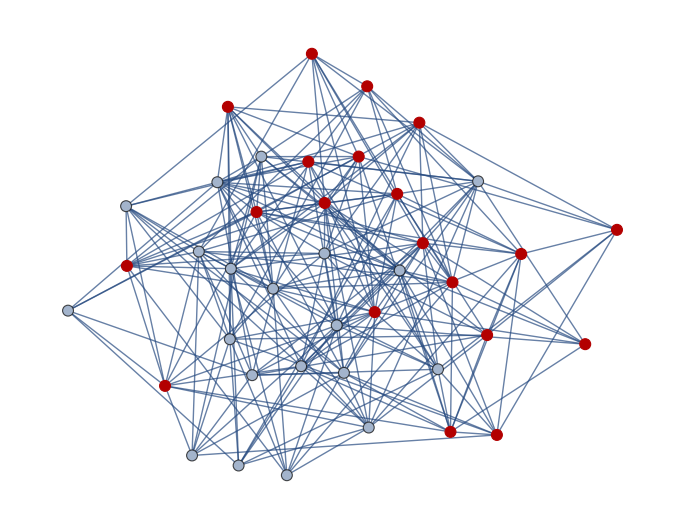

```mathematica
HighlightGraph[graph,Flatten[Union[List[#]]&@@@{2->2,3->3,5->5,6->6,9->9,11->11,13->13,15->15,17->17,19->19,20->20,24->24,25->25,28->28,31->31,33->33,36->36,37->18,38->26,40->40}]]
```

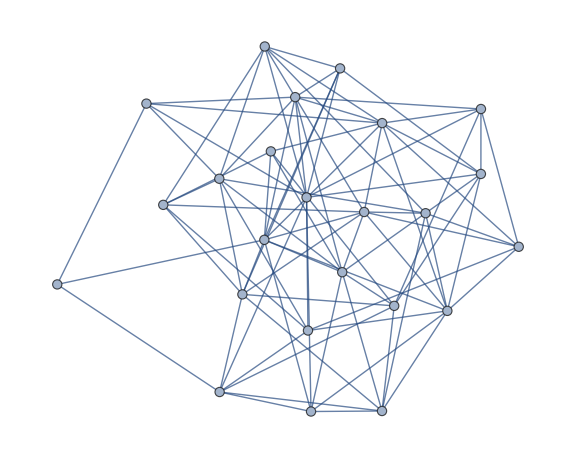

```mathematica
graph=RandomGraph[BernoulliGraphDistribution[24,0.3],ImageSize->Large]
```

```mathematica
Normal[First[FindSubgraphIsomorphism[Subgraph[graph,v_/;OddQ[VertexDegree[graph,v]]],graph]]]
```

{4→1,5→8,7→21,8→7,10→22,12→3,13→9,14→4,19→14,20→16,21→5,22→18}

```mathematica
Flatten[Union[List[#]]&@@@Normal[First[FindSubgraphIsomorphism[Subgraph[graph,v_/;OddQ[VertexDegree[graph,v]]],graph]]]]
```

{4,5,7,8,10,12,13,14,19,20,21,22}

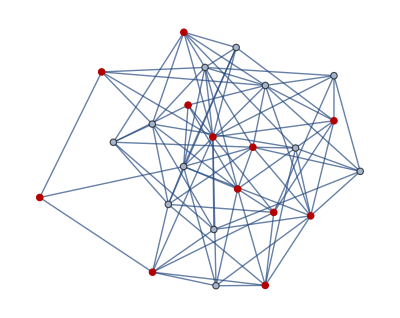

```mathematica
HighlightGraph[graph,Flatten[Union[List[#]]&@@@Normal[First[FindSubgraphIsomorphism[Subgraph[graph,v_/;OddQ[VertexDegree[graph,v]]],graph]]]],ImageSize->Full]
```

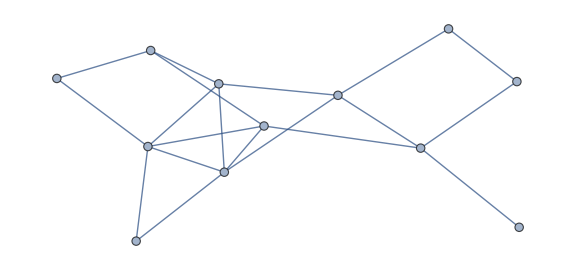

```mathematica
Subgraph[graph,v_/;OddQ[VertexDegree[graph,v]]]
```

```mathematica
RandomWeightedGraph[{vertices_,edges_},randomFunction_,options:OptionsPattern[]]:=Block[{randomGraph} ,randomGraph=RandomGraph[{vertices,edges},options];Graph[randomGraph,EdgeWeight->(Map[#->randomFunction[]&,EdgeList[randomGraph]])]];

RandomWeightedGraph[{vertices_,edges_},randomFunction_,k_?IntegerQ,options:OptionsPattern[]]:=Table[RandomWeightedGraph[{vertices,edges},randomFunction,options],k]

RandomWeightedGraph[{vertices_,edges_},randomFunction_,array_List,options:OptionsPattern[]]:=Array[RandomWeightedGraph[{vertices,edges},randomFunction,options]&,array]

RandomWeightedGraph[graphDistribution_,randomFunction_,options:OptionsPattern[]]:=Block[{randomGraph} ,randomGraph=RandomGraph[graphDistribution,options];Graph[randomGraph,EdgeWeight->(Map[#->randomFunction[]&,EdgeList[randomGraph]])]];

RandomWeightedGraph[graphDistribution_,randomFunction_,k_?IntegerQ,options:OptionsPattern[]]/;k>=1:=Table[RandomWeightedGraph[graphDistribution,randomFunction,options],k]

RandomWeightedGraph[graphDistribution_,randomFunction_,array_List,options:OptionsPattern[]]:=Array[RandomWeightedGraph[graphDistribution,randomFunction,options]&,array]
RandomWeightedGraph::usage="RandomWeightedGraph[{vertices, edges},  randomFunction] creates a random graph with vertices vertices and edges edges with edge weights given by randomFunction\nRandomWeightedGraph[{vertices, edges}, , randomFunction, k] creates k random graphs with vertices vertices and edges edges with edge weights given by randomFunction\nRandomWeightedGraph[{vertices, edges}, , randomFunction, array] creates a dimensions array of random graphs with vertices vertices and edges edges with edge weights given by randomFunction\nRandomWeightedGraph[distribution, , randomFunction] creates a random graph with graph distribution distribution with edge weights given by randomFunction\nRandomWeightedGraph[distribution, , randomFunction, k] creates k random graphs with graph distribution distribution with edge weights given by randomFunction\nRandomWeightedGraph[distribution, , randomFunction, array] creates a dimensions array of random graphs with graph distribution distribution with edge weights given by randomFunction";
```

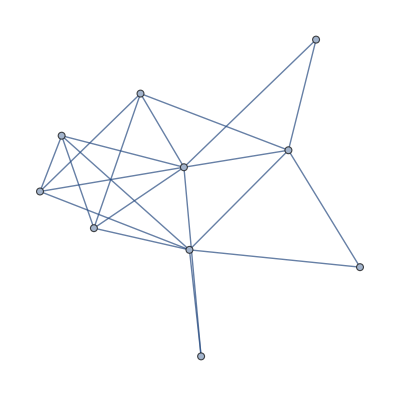

```mathematica
RandomWeightedGraph[{10,20},RandomInteger[{1,7}]]
```

```mathematica
EdgeWeightedGraphQ[RandomWeightedGraph[{10,20},RandomInteger[{1,7}]]]
```

True

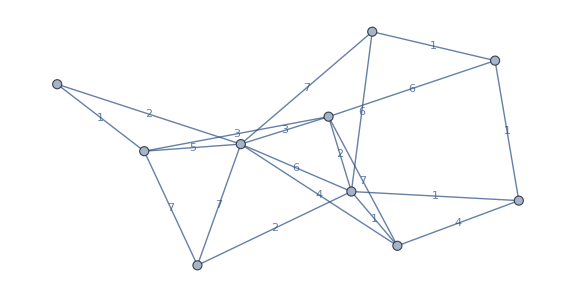

```mathematica
RandomWeightedGraph[{10,20},RandomInteger[{1,7}]&,ImageSize->Large,EdgeLabels->"EdgeWeight"]
```

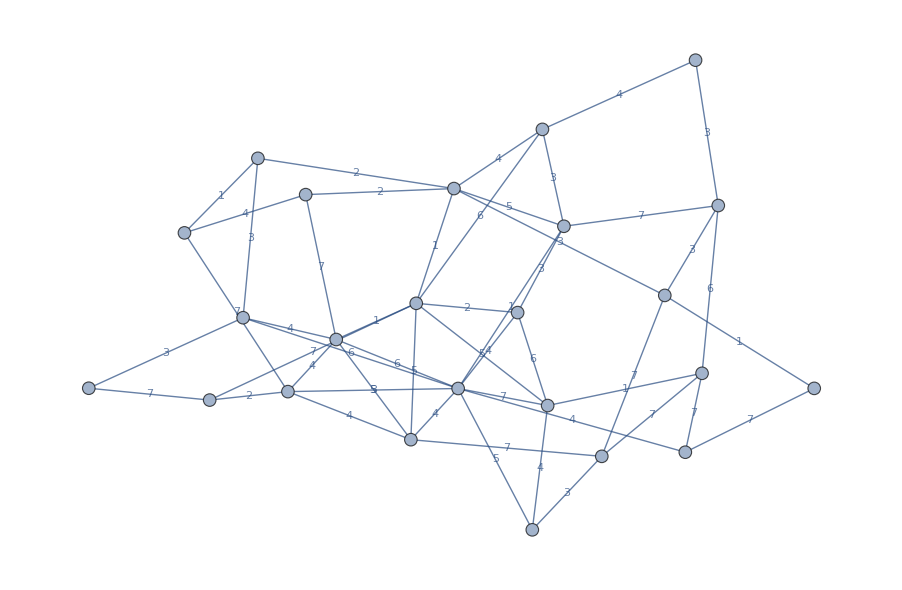

```mathematica
RandomWeightedGraph[BernoulliGraphDistribution[24,0.2],RandomInteger[{1,7}]&,ImageSize->Large,EdgeLabels->"EdgeWeight"]
```

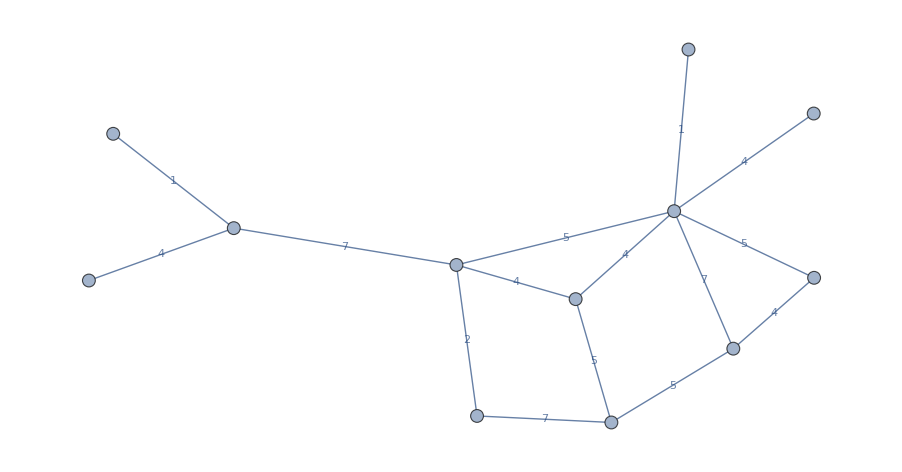

```mathematica
Subgraph[-Graphics-,x_/;OddQ[VertexDegree[-Graphics-,x]]]
```

```mathematica
AnnotationValue[-Graphics-,EdgeWeight]
```

{3,6,4,4,2,1,3,3,2,6,4,7,5,1,3,6,3,7,3,7,2,1,5,5,1,2,4,7,3,7,1,4,4,7,3,1,4,7,7,7,7,6,4,5,3,4,7,5,4,6}

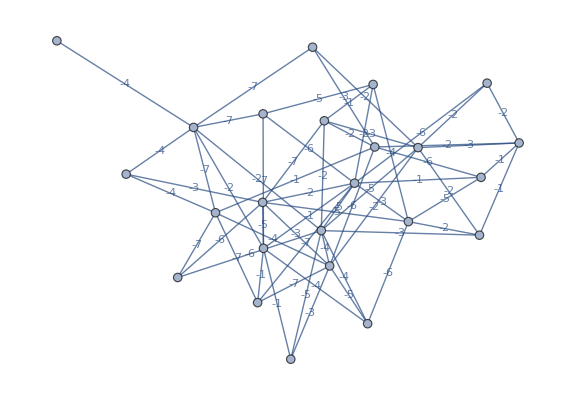

```mathematica
RandomWeightedGraph[BernoulliGraphDistribution[24,0.2],-RandomInteger[{1,7}]&,ImageSize->Large,EdgeLabels->"EdgeWeight"]
```

```mathematica
FindIndependentEdgeSet[RandomWeightedGraph[BernoulliGraphDistribution[24,0.2],-RandomInteger[{1,7}]&,ImageSize->Large,EdgeLabels->"EdgeWeight"]]
```

{1<->13,2<->24,3<->4,5<->23,6<->10,7<->9,8<->20,11<->19,12<->17,14<->18,15<->21,16<->22}

```mathematica
WeightedAdjacencyMatrix[RandomWeightedGraph[BernoulliGraphDistribution[24,0.2],RandomInteger[{1,7}]&,ImageSize->Large,EdgeLabels->"EdgeWeight"]]
```

SparseArray[…]

```mathematica
WeightedAdjacencyMatrix[RandomWeightedGraph[BernoulliGraphDistribution[24,0.2],RandomInteger[{1,7}]&,ImageSize->Large,EdgeLabels->"EdgeWeight"]]/.{0->∞}
```

SparseArray[…]

```mathematica
Normal[%87]
```

{{0,0,4,0,0,0,0,1,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,6,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,2,3,0,0},{4,0,0,0,0,0,0,0,0,0,2,0,0,0,1,5,0,0,0,3,0,0,0,0},{0,6,0,0,0,0,0,3,0,0,0,0,5,0,0,0,0,0,0,2,0,0,0,0},{0,0,0,0,0,0,0,0,0,6,0,0,0,0,0,0,0,0,5,0,0,0,0,0},{0,0,0,0,0,0,0,0,4,3,0,2,0,0,0,0,0,0,3,0,0,0,0,0},{0,3,0,0,0,0,0,0,0,0,2,0,2,0,0,0,0,0,7,0,3,0,7,5},{1,0,0,3,0,0,0,0,0,0,0,0,2,0,6,2,0,0,0,0,1,0,0,0},{0,0,0,0,0,4,0,0,0,0,0,6,0,0,0,0,0,0,0,0,0,7,0,0},{0,0,0,0,6,3,0,0,0,0,0,6,0,0,0,0,7,0,0,0,7,0,0,7},{0,0,2,0,0,0,2,0,0,0,0,0,0,0,0,0,0,3,0,0,7,0,2,4},{2,0,0,0,0,2,0,0,6,6,0,0,0,7,0,0,0,6,0,0,1,0,2,0},{0,0,0,5,0,0,2,2,0,0,0,0,0,1,0,0,0,0,0,4,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,7,1,0,0,0,2,6,0,6,0,0,0,1},{0,0,1,0,0,0,0,6,0,0,0,0,0,0,0,0,0,0,0,4,0,1,6,4},{0,0,5,0,0,0,0,2,0,0,0,0,0,0,0,0,0,2,0,0,3,0,0,1},{0,0,0,0,0,0,0,0,0,7,0,0,0,2,0,0,0,0,0,7,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,3,6,0,6,0,2,0,0,0,0,0,3,0,0},{0,0,0,0,5,3,7,0,0,0,0,0,0,0,0,0,0,0,0,0,4,0,6,0},{0,0,3,2,0,0,0,0,0,0,0,0,4,6,4,0,7,0,0,0,7,0,0,6},{0,2,0,0,0,0,3,1,0,7,7,1,0,0,0,3,0,0,4,7,0,0,1,0},{0,3,0,0,0,0,0,0,7,0,0,0,0,0,1,0,0,3,0,0,0,0,0,5},{0,0,0,0,0,0,7,0,0,0,2,2,0,0,6,0,0,0,6,0,1,0,0,0},{0,0,0,0,0,0,5,0,0,7,4,0,0,1,4,1,0,0,0,6,0,5,0,0}}

```mathematica
SparseArray[WeightedAdjacencyMatrix[RandomWeightedGraph[BernoulliGraphDistribution[24,0.2],RandomInteger[{1,7}]&,ImageSize->Large,EdgeLabels->"EdgeWeight"]],{24,24},∞]
```

SparseArray[…]

```mathematica
Normal[SparseArray[WeightedAdjacencyMatrix[RandomWeightedGraph[BernoulliGraphDistribution[24,0.2],RandomInteger[{1,7}]&,ImageSize->Large,EdgeLabels->"EdgeWeight"]],{24,24},∞]]
```

{{0,0,7,5,0,0,0,3,0,0,0,0,0,0,1,0,3,0,2,0,5,0,0,5},{0,0,0,0,0,0,0,0,0,0,0,0,0,3,1,0,0,0,0,0,0,0,0,6},{7,0,0,0,0,0,0,1,5,0,0,0,0,0,0,0,6,0,0,7,0,0,0,0},{5,0,0,0,1,0,0,5,0,0,0,0,0,3,0,0,0,0,0,0,6,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,4,0,7,0,4,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,4,0,0,0,0,1,0,0,0,5,0,0,0,3,2,6},{3,0,1,5,0,0,0,0,6,0,0,0,0,0,0,0,0,7,0,0,0,0,0,0},{0,0,5,0,0,0,4,6,0,0,5,0,0,6,2,0,0,5,0,2,0,0,7,0},{0,0,0,0,0,0,0,0,0,0,0,0,3,6,0,4,0,0,4,0,0,0,0,0},{0,0,0,0,0,0,0,0,5,0,0,6,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,6,0,0,0,0,7,0,0,0,0,0,0,2,0},{0,0,0,0,0,4,0,0,0,3,0,0,0,7,7,0,0,4,0,0,6,0,0,7},{0,3,0,3,0,0,1,0,6,6,0,0,7,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,7,0,0,2,0,0,0,7,0,0,4,0,0,0,0,0,4,7,7},{0,0,0,0,0,0,0,0,0,4,1,7,0,0,4,0,0,0,2,0,0,2,0,0},{3,0,6,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,0,6,7,0,3,0},{0,0,0,0,0,0,5,7,5,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0},{2,0,0,0,0,0,0,0,0,4,0,0,0,0,0,2,0,0,0,0,0,0,0,5},{0,0,7,0,0,0,0,0,2,0,0,0,0,0,0,0,6,0,0,0,0,0,0,5},{5,0,0,6,0,0,0,0,0,0,0,0,6,0,0,0,7,0,0,0,0,0,0,4},{0,0,0,0,0,0,3,0,0,0,0,0,0,0,4,2,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,2,0,7,0,0,2,0,0,7,0,3,0,0,0,0,0,0,0},{5,6,0,0,0,0,6,0,0,0,0,0,7,0,7,0,0,0,5,5,4,0,0,0}}

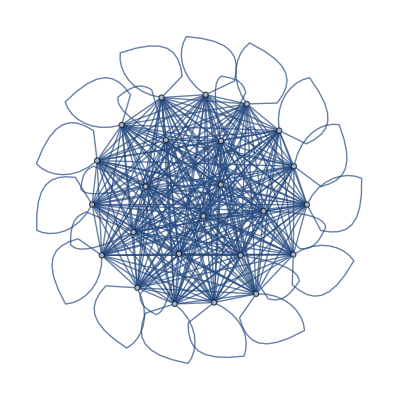

```mathematica
WeightedAdjacencyGraph[WeightedAdjacencyMatrix[RandomWeightedGraph[BernoulliGraphDistribution[24,0.2],RandomInteger[{1,7}]&,ImageSize->Large,EdgeLabels->"EdgeWeight"]]]
```

## Perfect Matching Graph

```mathematica
ClearAll[NegativeWeightsGraph]
NegativeWeightsGraph[graph_?GraphQ,options:OptionsPattern[Graph]]:=Block[{edgeWeights,edgelist},edgeWeights=AnnotationValue[graph,EdgeWeight];edgelist=EdgeList[graph];Graph[edgelist,EdgeWeight->-edgeWeights,options]]
```

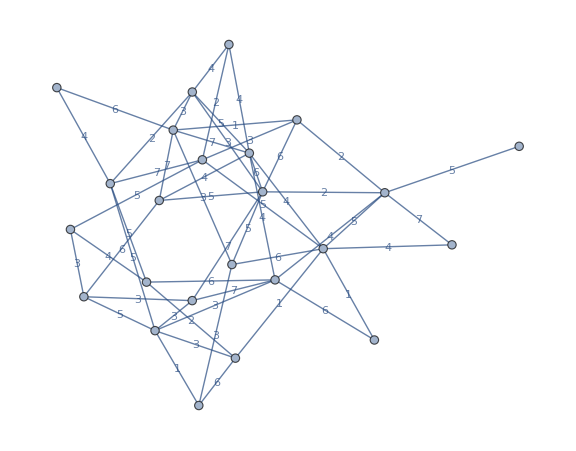

```mathematica
graph=RandomWeightedGraph[BernoulliGraphDistribution[24,0.2],RandomInteger[{1,7}]&,ImageSize->Large,EdgeLabels->"EdgeWeight"]
```

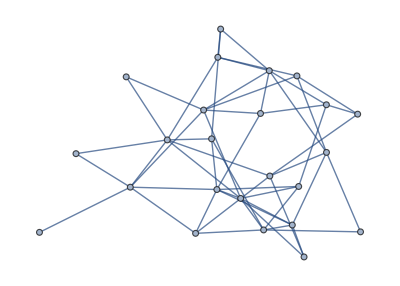

```mathematica
MinimumCostMatching[graph]
```

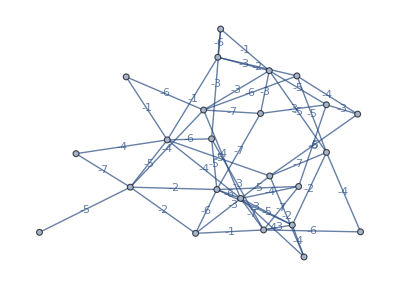

```mathematica
NegativeWeightsGraph[graph,EdgeLabels->"EdgeWeight"]
```

```mathematica
EdgeWeightedGraphQ[NegativeWeightsGraph[graph,EdgeLabels->"EdgeWeight"]]
```

True

```mathematica
EdgeWeightedGraphQ[NegativeWeightsGraph[graph]]
```

True

```mathematica
ClearAll[OddSubgraph]
OddSubgraph[graph_?GraphQ,options:OptionsPattern[Graph]]:=Subgraph[graph,x_/;OddQ[VertexDegree[graph,x]],options]
```

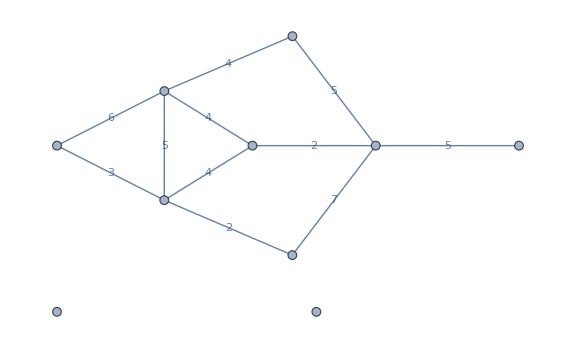

```mathematica
OddSubgraph[graph]
```

```mathematica
OddGraphMinimumCostMatching[graph_?GraphQ,options:OptionsPattern[Graph]]:=FindIndependentEdgeSet[NegativeWeightsGraph[OddSubgraph[graph]]]
```

```mathematica
OddGraphMinimumCostMatching[graph]
```

{}

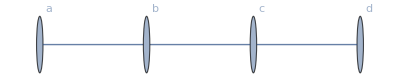

```mathematica
Graph[{a<->b,b<-> c,c<->d},VertexLabels->Automatic]
```

```mathematica
VertexDegree[Graph[{a<->b,b<-> c,c<->d},VertexLabels->Automatic]]
```

{1,2,2,1}

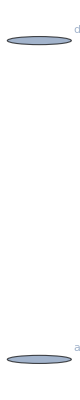

```mathematica
Subgraph[-Graphics-,x_/;OddQ[VertexDegree[-Graphics-,x]]]
```

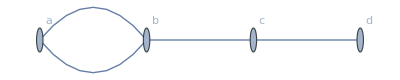

```mathematica
EdgeAdd[-Graphics-,{a<->b}]
```

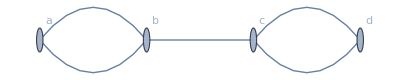

```mathematica
EdgeAdd[-Graphics-,{a<->b,c<->d}]
```

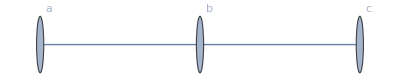
```mathematica
VertexDegree[EdgeAdd[-Graphics-,{a<->b,b<->c}]]
```

{2,4,2}

```mathematica
EulerianGraphQ[EdgeAdd[-Graphics-,{a<->b,b<->c}]]
```

True

```mathematica
VertexList[-Graphics-,x_/;OddQ[VertexDegree[-Graphics-,x]]]
```

{a,d}

```mathematica
EulerianGraphQ[Graph[{a<->b,b<-> c,c<->d},VertexLabels->Automatic]]
```

False

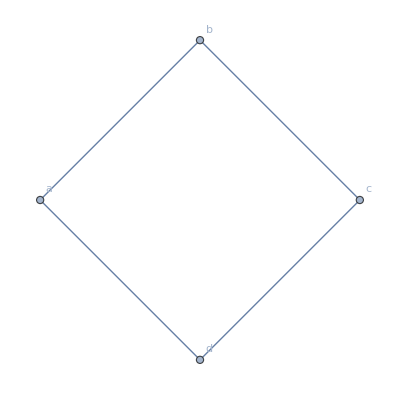

```mathematica
EulerizeGraph[Graph[{a<->b,b<-> c,c<->d},VertexLabels->Automatic]]
```

```mathematica
Subgraph[EulerizeGraph[Graph[{a<->b,b<-> c,c<->d},VertexLabels->Automatic]],Graph[{a<->b,b<-> c,c<->d},VertexLabels->Automatic]]
```

-Graphics-

```mathematica
OddSubgraph[graph]
```

-Graphics-

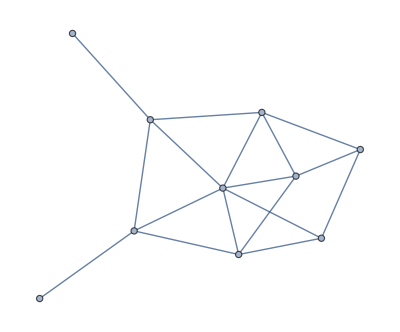

```mathematica
graph=RandomGraph[BernoulliGraphDistribution[10,0.4]]
```

```mathematica
ConnectedGraphQ[graph]
```

True

```mathematica
PlanarGraphQ[graph]
```

False

```mathematica
VertexList[graph,x_/;OddQ[VertexDegree[graph,x]]]
```

{1,2,3,8}

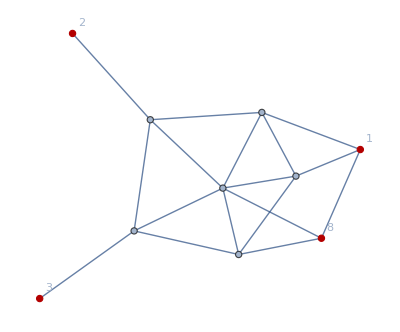

```mathematica
HighlightGraph[graph,VertexList[graph,x_/;OddQ[VertexDegree[graph,x]]],VertexLabels->Automatic]
```

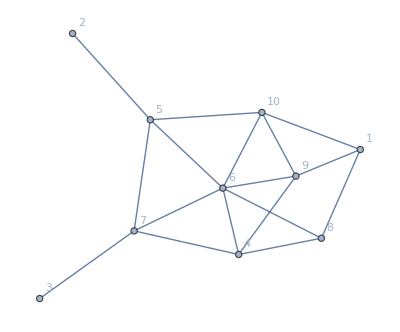

```mathematica
Graph[graph,VertexLabels->Automatic]
```

```mathematica
GraphQ[graph]
```

True

```mathematica
FindPath[graph,3,8]
```

{}

```mathematica
FindEdgeIndependentPaths[graph,3,8,1]
```

{{3,7,6,8}}

```mathematica
FindEdgeIndependentPaths[graph,3,8,2]
```

{{3,7,6,8}}

```mathematica
FindVertexIndependentPaths[graph,3,8,2]
```

{{3,7,6,8}}

```mathematica
InputForm[graph]
```

Graph[{1, 2, 3, 4, 5, 6, 7, 8, 9, 10}, {Null, SparseArray[Automatic, {10, 10}, 0, 
   {1, {{0, 3, 4, 5, 9, 12, 16, 16, 16, 17, 17}, {{8}, {9}, {10}, {5}, {7}, {6}, {7}, {8}, {9}, {6}, {7}, {10}, {7}, {8}, {9}, {10}, {10}}}, 
    {1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1}}]}]

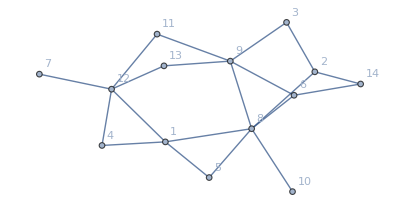

```mathematica
graph=RandomGraph[{14,20},VertexLabels->Automatic]
```

```mathematica
FindPath[graph,1,3]
```

{{1,2,4,3}}

```mathematica
FindPath[graph,1,3,Infinity,All]
```

{{1,10,6,3},{1,10,4,3},{1,9,6,3},{1,8,5,3},{1,2,4,3},{1,10,7,6,3},{1,10,7,5,3},{1,10,6,5,3},{1,10,2,4,3},{1,9,8,5,3},{1,9,6,5,3},{1,8,9,6,3},{1,8,5,6,3},{1,8,2,4,3},{1,2,10,6,3},{1,2,10,4,3},{1,2,8,5,3},{1,2,7,6,3},{1,2,7,5,3},{1,10,7,6,5,3},{1,10,7,5,6,3},{1,10,7,2,4,3},{1,10,6,7,5,3},{1,10,2,8,5,3},{1,10,2,7,6,3},{1,10,2,7,5,3},{1,9,8,5,6,3},{1,9,8,2,4,3},{1,9,6,10,4,3},{1,9,6,7,5,3},{1,8,9,6,5,3},{1,8,5,7,6,3},{1,8,2,10,6,3},{1,8,2,10,4,3},{1,8,2,7,6,3},{1,8,2,7,5,3},{1,2,10,7,6,3},{1,2,10,7,5,3},{1,2,10,6,5,3},{1,2,8,9,6,3},{1,2,8,5,6,3},{1,2,7,10,6,3},{1,2,7,10,4,3},{1,2,7,6,5,3},{1,2,7,5,6,3},{1,2,4,10,6,3},{1,10,7,2,8,5,3},{1,10,6,9,8,5,3},{1,10,6,7,2,4,3},{1,10,4,2,8,5,3},{1,10,4,2,7,6,3},{1,10,4,2,7,5,3},{1,10,2,8,9,6,3},{1,10,2,8,5,6,3},{1,10,2,7,6,5,3},{1,10,2,7,5,6,3},{1,9,8,5,7,6,3},{1,9,8,2,10,6,3},{1,9,8,2,10,4,3},{1,9,8,2,7,6,3},{1,9,8,2,7,5,3},{1,9,6,10,7,5,3},{1,9,6,10,2,4,3},{1,9,6,7,10,4,3},{1,9,6,7,2,4,3},{1,8,9,6,10,4,3},{1,8,9,6,7,5,3},{1,8,5,7,10,6,3},{1,8,5,7,10,4,3},{1,8,5,7,2,4,3},{1,8,5,6,10,4,3},{1,8,2,10,7,6,3},{1,8,2,10,7,5,3},{1,8,2,10,6,5,3},{1,8,2,7,10,6,3},{1,8,2,7,10,4,3},{1,8,2,7,6,5,3},{1,8,2,7,5,6,3},{1,8,2,4,10,6,3},{1,2,10,7,6,5,3},{1,2,10,7,5,6,3},{1,2,10,6,7,5,3},{1,2,8,9,6,5,3},{1,2,8,5,7,6,3},{1,2,7,10,6,5,3},{1,2,7,6,10,4,3},{1,2,4,10,7,6,3},{1,2,4,10,7,5,3},{1,2,4,10,6,5,3},{1,10,7,6,9,8,5,3},{1,10,7,5,8,9,6,3},{1,10,7,5,8,2,4,3},{1,10,7,2,8,9,6,3},{1,10,7,2,8,5,6,3},{1,10,6,9,8,2,4,3},{1,10,6,7,2,8,5,3},{1,10,6,5,8,2,4,3},{1,10,6,5,7,2,4,3},{1,10,4,2,8,9,6,3},{1,10,4,2,8,5,6,3},{1,10,4,2,7,6,5,3},{1,10,4,2,7,5,6,3},{1,10,2,8,9,6,5,3},{1,10,2,8,5,7,6,3},{1,9,8,5,7,10,6,3},{1,9,8,5,7,10,4,3},{1,9,8,5,7,2,4,3},{1,9,8,5,6,10,4,3},{1,9,8,2,10,7,6,3},{1,9,8,2,10,7,5,3},{1,9,8,2,10,6,5,3},{1,9,8,2,7,10,6,3},{1,9,8,2,7,10,4,3},{1,9,8,2,7,6,5,3},{1,9,8,2,7,5,6,3},{1,9,8,2,4,10,6,3},{1,9,6,10,7,2,4,3},{1,9,6,10,2,8,5,3},{1,9,6,10,2,7,5,3},{1,9,6,7,10,2,4,3},{1,9,6,7,2,10,4,3},{1,9,6,7,2,8,5,3},{1,9,6,5,8,2,4,3},{1,9,6,5,7,10,4,3},{1,9,6,5,7,2,4,3},{1,8,9,6,10,7,5,3},{1,8,9,6,10,2,4,3},{1,8,9,6,7,10,4,3},{1,8,9,6,7,2,4,3},{1,8,5,7,10,2,4,3},{1,8,5,7,6,10,4,3},{1,8,5,7,2,10,6,3},{1,8,5,7,2,10,4,3},{1,8,5,6,10,2,4,3},{1,8,5,6,7,10,4,3},{1,8,5,6,7,2,4,3},{1,8,2,10,7,6,5,3},{1,8,2,10,7,5,6,3},{1,8,2,10,6,7,5,3},{1,8,2,7,10,6,5,3},{1,8,2,7,6,10,4,3},{1,8,2,4,10,7,6,3},{1,8,2,4,10,7,5,3},{1,8,2,4,10,6,5,3},{1,2,10,6,9,8,5,3},{1,2,8,9,6,10,4,3},{1,2,8,9,6,7,5,3},{1,2,8,5,7,10,6,3},{1,2,8,5,7,10,4,3},{1,2,8,5,6,10,4,3},{1,2,7,6,9,8,5,3},{1,2,7,5,8,9,6,3},{1,2,7,5,6,10,4,3},{1,2,4,10,7,6,5,3},{1,2,4,10,7,5,6,3},{1,2,4,10,6,7,5,3},{1,10,7,6,9,8,2,4,3},{1,10,7,6,5,8,2,4,3},{1,10,7,2,8,9,6,5,3},{1,10,6,9,8,2,7,5,3},{1,10,6,7,5,8,2,4,3},{1,10,4,2,8,9,6,5,3},{1,10,4,2,8,5,7,6,3},{1,10,2,8,9,6,7,5,3},{1,10,2,7,6,9,8,5,3},{1,10,2,7,5,8,9,6,3},{1,9,8,5,7,10,2,4,3},{1,9,8,5,7,6,10,4,3},{1,9,8,5,7,2,10,6,3},{1,9,8,5,7,2,10,4,3},{1,9,8,5,6,10,2,4,3},{1,9,8,5,6,7,10,4,3},{1,9,8,5,6,7,2,4,3},{1,9,8,2,10,7,6,5,3},{1,9,8,2,10,7,5,6,3},{1,9,8,2,10,6,7,5,3},{1,9,8,2,7,10,6,5,3},{1,9,8,2,7,6,10,4,3},{1,9,8,2,4,10,7,6,3},{1,9,8,2,4,10,7,5,3},{1,9,8,2,4,10,6,5,3},{1,9,6,10,7,2,8,5,3},{1,9,6,10,4,2,8,5,3},{1,9,6,10,4,2,7,5,3},{1,9,6,7,10,2,8,5,3},{1,9,6,7,5,8,2,4,3},{1,9,6,5,8,2,10,4,3},{1,9,6,5,7,10,2,4,3},{1,9,6,5,7,2,10,4,3},{1,8,9,6,10,7,2,4,3},{1,8,9,6,10,2,7,5,3},{1,8,9,6,7,10,2,4,3},{1,8,9,6,7,2,10,4,3},{1,8,9,6,5,7,10,4,3},{1,8,9,6,5,7,2,4,3},{1,8,5,7,6,10,2,4,3},{1,8,5,7,2,4,10,6,3},{1,8,5,6,10,7,2,4,3},{1,8,5,6,7,10,2,4,3},{1,8,5,6,7,2,10,4,3},{1,8,2,7,5,6,10,4,3},{1,8,2,4,10,7,6,5,3},{1,8,2,4,10,7,5,6,3},{1,8,2,4,10,6,7,5,3},{1,2,10,7,6,9,8,5,3},{1,2,10,7,5,8,9,6,3},{1,2,8,9,6,10,7,5,3},{1,2,8,9,6,7,10,4,3},{1,2,8,5,7,6,10,4,3},{1,2,8,5,6,7,10,4,3},{1,2,7,10,6,9,8,5,3},{1,2,4,10,6,9,8,5,3},{1,10,7,5,6,9,8,2,4,3},{1,10,6,9,8,5,7,2,4,3},{1,10,4,2,8,9,6,7,5,3},{1,10,4,2,7,6,9,8,5,3},{1,10,4,2,7,5,8,9,6,3},{1,9,8,5,7,6,10,2,4,3},{1,9,8,5,7,2,4,10,6,3},{1,9,8,5,6,10,7,2,4,3},{1,9,8,5,6,7,10,2,4,3},{1,9,8,5,6,7,2,10,4,3},{1,9,8,2,7,5,6,10,4,3},{1,9,8,2,4,10,7,6,5,3},{1,9,8,2,4,10,7,5,6,3},{1,9,8,2,4,10,6,7,5,3},{1,9,6,10,7,5,8,2,4,3},{1,9,6,7,10,4,2,8,5,3},{1,9,6,7,5,8,2,10,4,3},{1,9,6,5,8,2,7,10,4,3},{1,8,9,6,10,4,2,7,5,3},{1,8,9,6,5,7,10,2,4,3},{1,8,9,6,5,7,2,10,4,3},{1,2,8,9,6,5,7,10,4,3},{1,2,7,5,8,9,6,10,4,3},{1,2,4,10,7,6,9,8,5,3},{1,2,4,10,7,5,8,9,6,3}}

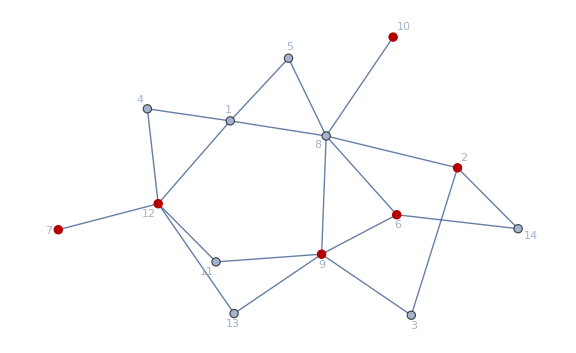

```mathematica
HighlightGraph[graph,VertexList[graph,x_/;OddQ[VertexDegree[graph,x]]],ImageSize->Large,GraphLayout->"SpringEmbedding"]
```

```mathematica
FindEdgeIndependentPaths[graph,10,2,1]
```

{{10,8,2}}

```mathematica
FindVertexIndependentPaths[graph,10,2,2]
```

{{10,8,2}}

```mathematica
FindPath[graph,10,2,Infinity,All]
```

{{10,8,2},{10,8,9,3,2},{10,8,6,14,2},{10,8,9,6,14,2},{10,8,6,9,3,2},{10,8,1,12,13,9,3,2},{10,8,1,12,11,9,3,2},{10,8,5,1,12,13,9,3,2},{10,8,5,1,12,11,9,3,2},{10,8,1,12,13,9,6,14,2},{10,8,1,12,11,9,6,14,2},{10,8,1,4,12,13,9,3,2},{10,8,1,4,12,11,9,3,2},{10,8,5,1,12,13,9,6,14,2},{10,8,5,1,12,11,9,6,14,2},{10,8,5,1,4,12,13,9,3,2},{10,8,5,1,4,12,11,9,3,2},{10,8,1,4,12,13,9,6,14,2},{10,8,1,4,12,11,9,6,14,2},{10,8,5,1,4,12,13,9,6,14,2},{10,8,5,1,4,12,11,9,6,14,2}}

```mathematica
FindShortestPath[graph,10,2]
```

{10,8,2}

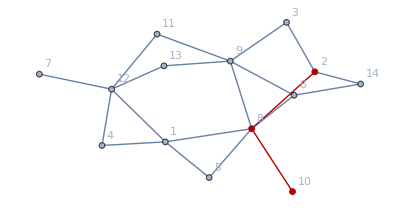

```mathematica
HighlightGraph[Graph[{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{Null,SparseArray[Automatic,{14,14},0,{1,{{0,4,7,9,11,13,16,17,23,28,29,31,36,38,40},{{4},{5},{8},{12},{3},{8},{14},{2},{9},{1},{12},{1},{8},{8},{9},{14},{12},{1},{2},{5},{6},{9},{10},{3},{6},{8},{11},{13},{8},{9},{12},{1},{4},{7},{11},{13},{9},{12},{2},{6}}},Pattern}]},{VertexLabels->{Automatic}}],PathGraph[{10,8,2}]]
```

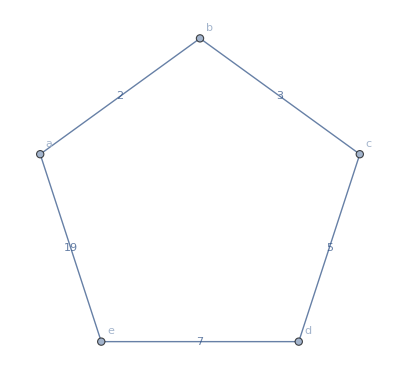

```mathematica
Graph[{a,b,c,d,e},{a<->b,b<->c,c<->d,d<->e,a<->e},VertexLabels->Automatic,EdgeWeight->Thread[{a<->b,b<->c,c<->d,d<->e,a<->e}->{2,3,5,7,19}],EdgeLabels->"EdgeWeight"]
```

```mathematica
FindShortestPath[Graph[{a,b,c,d,e},{a<->b,b<->c,c<->d,d<->e,a<->e},VertexLabels->Automatic,EdgeWeight->Thread[{a<->b,b<->c,c<->d,d<->e,a<->e}->{2,3,5,7,19}]],a,e]
```

{a,b,c,d,e}

## Find the odd vertices

```mathematica
OddVertices[graph_?GraphQ]:=VertexList[graph,x_/;OddQ[VertexDegree[graph,x]]]
```

```mathematica
OddVertices[graph]
```

{2,6,7,9,10,12}

```mathematica
Subsets[OddVertices[graph],{2}]
```

{{2,6},{2,7},{2,9},{2,10},{2,12},{6,7},{6,9},{6,10},{6,12},{7,9},{7,10},{7,12},{9,10},{9,12},{10,12}}

```mathematica
Groupings[Table[s,4],Construct->2]
```

{s[s][s][s],s[s[s][s]],s[s[s]][s],s[s[s[s]]],s[s][s[s]]}

```mathematica
Groupings[Table[s,12],Construct->3]
```

{}

```mathematica
Groupings[{a,b,c,d},Construct->2]
```

{a[b][c][d],a[b[c][d]],a[b[c]][d],a[b[c[d]]],a[b][c[d]]}

```mathematica
Groupings[{a,b,c,d},2]
```

{{{{a,b},c},d},{a,{{b,c},d}},{{a,{b,c}},d},{a,{b,{c,d}}},{{a,b},{c,d}}}

```mathematica
Permutations[{a,b,c,d},{4}]
```

{{a,b,c,d},{a,b,d,c},{a,c,b,d},{a,c,d,b},{a,d,b,c},{a,d,c,b},{b,a,c,d},{b,a,d,c},{b,c,a,d},{b,c,d,a},{b,d,a,c},{b,d,c,a},{c,a,b,d},{c,a,d,b},{c,b,a,d},{c,b,d,a},{c,d,a,b},{c,d,b,a},{d,a,b,c},{d,a,c,b},{d,b,a,c},{d,b,c,a},{d,c,a,b},{d,c,b,a}}

```mathematica
Partition[#,2]&/@Permutations[{a,b,c,d},{4}]
```

{{{a,b},{c,d}},{{a,b},{d,c}},{{a,c},{b,d}},{{a,c},{d,b}},{{a,d},{b,c}},{{a,d},{c,b}},{{b,a},{c,d}},{{b,a},{d,c}},{{b,c},{a,d}},{{b,c},{d,a}},{{b,d},{a,c}},{{b,d},{c,a}},{{c,a},{b,d}},{{c,a},{d,b}},{{c,b},{a,d}},{{c,b},{d,a}},{{c,d},{a,b}},{{c,d},{b,a}},{{d,a},{b,c}},{{d,a},{c,b}},{{d,b},{a,c}},{{d,b},{c,a}},{{d,c},{a,b}},{{d,c},{b,a}}}

```mathematica
DeleteDuplicates[Flatten[Partition[#,2]&/@Permutations[{a,b,c,d},{4}],{1}]]
```

{{{a,b},{c,d}},{{a,b},{d,c}},{{a,c},{b,d}},{{a,c},{d,b}},{{a,d},{b,c}},{{a,d},{c,b}},{{b,a},{c,d}},{{b,a},{d,c}},{{b,c},{a,d}},{{b,c},{d,a}},{{b,d},{a,c}},{{b,d},{c,a}},{{c,a},{b,d}},{{c,a},{d,b}},{{c,b},{a,d}},{{c,b},{d,a}},{{c,d},{a,b}},{{c,d},{b,a}},{{d,a},{b,c}},{{d,a},{c,b}},{{d,b},{a,c}},{{d,b},{c,a}},{{d,c},{a,b}},{{d,c},{b,a}}}

```mathematica
Subsets[{a,b,c,d},{4}]
```

{{a,b,c,d}}

```mathematica
Subsets[{a,b,c,d},{2},3]
```

{{a,b},{a,c},{a,d}}

```mathematica
Subsets[{d,c,b,a},{2},3]
```

{{d,c},{d,b},{d,a}}

```mathematica
Subsets[Reverse[{a,b,c,d}],{2},3]
```

{{d,c},{d,b},{d,a}}

```mathematica
Reverse[Subsets[Reverse[{a,b,c,d}],{2},3]]
```

{{d,a},{d,b},{d,c}}

```mathematica
{#1,#2}&[{a,b},{d,c}]
```

{{a,b},{d,c}}

```mathematica
{#1,#2}&@@{{a,b},{d,c}}
```

{{a,b},{d,c}}

```mathematica
Join[Subsets[{a,b,c,d},{2}],Subsets[Reverse[{a,b,c,d}],{2}]]
```

{{a,b},{a,c},{a,d},{b,c},{b,d},{c,d},{d,c},{d,b},{d,a},{c,b},{c,a},{b,a}}

```mathematica
List[Subsets[{a,b,c,d},{2}],Subsets[Reverse[{a,b,c,d}],{2}]]
```

{{{a,b},{a,c},{a,d},{b,c},{b,d},{c,d}},{{d,c},{d,b},{d,a},{c,b},{c,a},{b,a}}}

```mathematica
Transpose[List[Subsets[{a,b,c,d},{2},3],Reverse[Subsets[Reverse[{a,b,c,d}],{2},3]]]]
```

{{{a,b},{d,c}},{{a,c},{d,b}},{{a,d},{d,a}}}

```mathematica
Subsets[{a,b,c,d},{2}]
```

{{a,b},{a,c},{a,d},{b,c},{b,d},{c,d}}

```mathematica
TakeDrop[Subsets[{a,b,c,d},{2}],3]
```

{{{a,b},{a,c},{a,d}},{{b,c},{b,d},{c,d}}}

```mathematica
MapAt[Reverse,TakeDrop[Subsets[{a,b,c,d},{2}],3],2]
```

{{{a,b},{a,c},{a,d}},{{c,d},{b,d},{b,c}}}

```mathematica
Transpose[MapAt[Reverse,TakeDrop[Subsets[{a,b,c,d},{2}],3],2]]
```

{{{a,b},{c,d}},{{a,c},{b,d}},{{a,d},{b,c}}}

```mathematica
Binomial[4,2]/2
```

3

```mathematica
Binomial[6,2]
```

15

```mathematica
Subsets[Range[6],{2}]
```

{{1,2},{1,3},{1,4},{1,5},{1,6},{2,3},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{4,5},{4,6},{5,6}}

```mathematica
Take[Subsets[Range[6],{2}],7]
```

{{1,2},{1,3},{1,4},{1,5},{1,6},{2,3},{2,4}}

```mathematica
Length[Subsets[Range[6],{2}]]
```

15

```mathematica
Transpose[MapAt[Reverse,TakeDrop[Subsets[{a,b,c,d,e,f},{2}],2],2]]
```

Transpose::nmtx: The first two levels of {{{a,b},{a,c}},{{e,f},{d,f},{d,e},{c,f},{c,e},{c,d},{b,f},{b,e},{b,d},{b,c},«3»}} cannot be transposed.

Transpose[{{{a,b},{a,c}},{{e,f},{d,f},{d,e},{c,f},{c,e},{c,d},{b,f},{b,e},{b,d},{b,c},{a,f},{a,e},{a,d}}}]

```mathematica
TakeDrop[Subsets[{a,b,c,d,e,f},{3}],2]
```

{{{a,b,c},{a,b,d}},{{a,b,e},{a,b,f},{a,c,d},{a,c,e},{a,c,f},{a,d,e},{a,d,f},{a,e,f},{b,c,d},{b,c,e},{b,c,f},{b,d,e},{b,d,f},{b,e,f},{c,d,e},{c,d,f},{c,e,f},{d,e,f}}}

```mathematica
Subsets[{a,b,c,d,e,f},{3}]
```

{{a,b,c},{a,b,d},{a,b,e},{a,b,f},{a,c,d},{a,c,e},{a,c,f},{a,d,e},{a,d,f},{a,e,f},{b,c,d},{b,c,e},{b,c,f},{b,d,e},{b,d,f},{b,e,f},{c,d,e},{c,d,f},{c,e,f},{d,e,f}}

```mathematica
Partition[Subsets[{a,b,c,d,e,f},{3}],10]
```

{{{a,b,c},{a,b,d},{a,b,e},{a,b,f},{a,c,d},{a,c,e},{a,c,f},{a,d,e},{a,d,f},{a,e,f}},{{b,c,d},{b,c,e},{b,c,f},{b,d,e},{b,d,f},{b,e,f},{c,d,e},{c,d,f},{c,e,f},{d,e,f}}}

```mathematica
Binomial[6,3]/2
```

10

```mathematica
TakeDrop[Subsets[{a,b,c,d,e,f},{3}],10]
```

{{{a,b,c},{a,b,d},{a,b,e},{a,b,f},{a,c,d},{a,c,e},{a,c,f},{a,d,e},{a,d,f},{a,e,f}},{{b,c,d},{b,c,e},{b,c,f},{b,d,e},{b,d,f},{b,e,f},{c,d,e},{c,d,f},{c,e,f},{d,e,f}}}

```mathematica
MapAt[Reverse,TakeDrop[Subsets[{a,b,c,d,e,f},{3}],10],2]
```

{{{a,b,c},{a,b,d},{a,b,e},{a,b,f},{a,c,d},{a,c,e},{a,c,f},{a,d,e},{a,d,f},{a,e,f}},{{d,e,f},{c,e,f},{c,d,f},{c,d,e},{b,e,f},{b,d,f},{b,d,e},{b,c,f},{b,c,e},{b,c,d}}}

```mathematica
Transpose[MapAt[Reverse,TakeDrop[Subsets[{a,b,c,d},{2}],3],2]]
```

{{{a,b},{c,d}},{{a,c},{b,d}},{{a,d},{b,c}}}

```mathematica
Transpose[MapAt[Reverse,TakeDrop[Subsets[{a,b,c,d,e,f},{3}],10],2]]
```

{{{a,b,c},{d,e,f}},{{a,b,d},{c,e,f}},{{a,b,e},{c,d,f}},{{a,b,f},{c,d,e}},{{a,c,d},{b,e,f}},{{a,c,e},{b,d,f}},{{a,c,f},{b,d,e}},{{a,d,e},{b,c,f}},{{a,d,f},{b,c,e}},{{a,e,f},{b,c,d}}}

```mathematica
Transpose[MapAt[Reverse,TakeDrop[Subsets[{a,b,c,d,e,f},{3}],Binomial[6,3]/2],2]]
```

{{{a,b,c},{d,e,f}},{{a,b,d},{c,e,f}},{{a,b,e},{c,d,f}},{{a,b,f},{c,d,e}},{{a,c,d},{b,e,f}},{{a,c,e},{b,d,f}},{{a,c,f},{b,d,e}},{{a,d,e},{b,c,f}},{{a,d,f},{b,c,e}},{{a,e,f},{b,c,d}}}

```mathematica
Transpose[MapAt[Reverse,TakeDrop[Subsets[{a,b,c,d,e,f,g,h},{4}],Binomial[8,4]/2],2]]
```

{{{a,b,c,d},{e,f,g,h}},{{a,b,c,e},{d,f,g,h}},{{a,b,c,f},{d,e,g,h}},{{a,b,c,g},{d,e,f,h}},{{a,b,c,h},{d,e,f,g}},{{a,b,d,e},{c,f,g,h}},{{a,b,d,f},{c,e,g,h}},{{a,b,d,g},{c,e,f,h}},{{a,b,d,h},{c,e,f,g}},{{a,b,e,f},{c,d,g,h}},{{a,b,e,g},{c,d,f,h}},{{a,b,e,h},{c,d,f,g}},{{a,b,f,g},{c,d,e,h}},{{a,b,f,h},{c,d,e,g}},{{a,b,g,h},{c,d,e,f}},{{a,c,d,e},{b,f,g,h}},{{a,c,d,f},{b,e,g,h}},{{a,c,d,g},{b,e,f,h}},{{a,c,d,h},{b,e,f,g}},{{a,c,e,f},{b,d,g,h}},{{a,c,e,g},{b,d,f,h}},{{a,c,e,h},{b,d,f,g}},{{a,c,f,g},{b,d,e,h}},{{a,c,f,h},{b,d,e,g}},{{a,c,g,h},{b,d,e,f}},{{a,d,e,f},{b,c,g,h}},{{a,d,e,g},{b,c,f,h}},{{a,d,e,h},{b,c,f,g}},{{a,d,f,g},{b,c,e,h}},{{a,d,f,h},{b,c,e,g}},{{a,d,g,h},{b,c,e,f}},{{a,e,f,g},{b,c,d,h}},{{a,e,f,h},{b,c,d,g}},{{a,e,g,h},{b,c,d,f}},{{a,f,g,h},{b,c,d,e}}}

```mathematica
MapAt[Reverse,TakeDrop[Subsets[{a,b,c,d,e,f,g,h},{4}],Binomial[8,4]/2],2]
```

{{{a,b,c,d},{a,b,c,e},{a,b,c,f},{a,b,c,g},{a,b,c,h},{a,b,d,e},{a,b,d,f},{a,b,d,g},{a,b,d,h},{a,b,e,f},{a,b,e,g},{a,b,e,h},{a,b,f,g},{a,b,f,h},{a,b,g,h},{a,c,d,e},{a,c,d,f},{a,c,d,g},{a,c,d,h},{a,c,e,f},{a,c,e,g},{a,c,e,h},{a,c,f,g},{a,c,f,h},{a,c,g,h},{a,d,e,f},{a,d,e,g},{a,d,e,h},{a,d,f,g},{a,d,f,h},{a,d,g,h},{a,e,f,g},{a,e,f,h},{a,e,g,h},{a,f,g,h}},{{e,f,g,h},{d,f,g,h},{d,e,g,h},{d,e,f,h},{d,e,f,g},{c,f,g,h},{c,e,g,h},{c,e,f,h},{c,e,f,g},{c,d,g,h},{c,d,f,h},{c,d,f,g},{c,d,e,h},{c,d,e,g},{c,d,e,f},{b,f,g,h},{b,e,g,h},{b,e,f,h},{b,e,f,g},{b,d,g,h},{b,d,f,h},{b,d,f,g},{b,d,e,h},{b,d,e,g},{b,d,e,f},{b,c,g,h},{b,c,f,h},{b,c,f,g},{b,c,e,h},{b,c,e,g},{b,c,e,f},{b,c,d,h},{b,c,d,g},{b,c,d,f},{b,c,d,e}}}

```mathematica
Transpose[MapAt[Reverse,TakeDrop[Subsets[{a,b,c,d,e,f,g,h},{4}],Binomial[8,4]/2],2],{3,1,2}]
```

{{{a,e},{b,f},{c,g},{d,h}},{{a,d},{b,f},{c,g},{e,h}},{{a,d},{b,e},{c,g},{f,h}},{{a,d},{b,e},{c,f},{g,h}},{{a,d},{b,e},{c,f},{h,g}},{{a,c},{b,f},{d,g},{e,h}},{{a,c},{b,e},{d,g},{f,h}},{{a,c},{b,e},{d,f},{g,h}},{{a,c},{b,e},{d,f},{h,g}},{{a,c},{b,d},{e,g},{f,h}},{{a,c},{b,d},{e,f},{g,h}},{{a,c},{b,d},{e,f},{h,g}},{{a,c},{b,d},{f,e},{g,h}},{{a,c},{b,d},{f,e},{h,g}},{{a,c},{b,d},{g,e},{h,f}},{{a,b},{c,f},{d,g},{e,h}},{{a,b},{c,e},{d,g},{f,h}},{{a,b},{c,e},{d,f},{g,h}},{{a,b},{c,e},{d,f},{h,g}},{{a,b},{c,d},{e,g},{f,h}},{{a,b},{c,d},{e,f},{g,h}},{{a,b},{c,d},{e,f},{h,g}},{{a,b},{c,d},{f,e},{g,h}},{{a,b},{c,d},{f,e},{h,g}},{{a,b},{c,d},{g,e},{h,f}},{{a,b},{d,c},{e,g},{f,h}},{{a,b},{d,c},{e,f},{g,h}},{{a,b},{d,c},{e,f},{h,g}},{{a,b},{d,c},{f,e},{g,h}},{{a,b},{d,c},{f,e},{h,g}},{{a,b},{d,c},{g,e},{h,f}},{{a,b},{e,c},{f,d},{g,h}},{{a,b},{e,c},{f,d},{h,g}},{{a,b},{e,c},{g,d},{h,f}},{{a,b},{f,c},{g,d},{h,e}}}

```mathematica
Transpose[MapAt[Reverse,TakeDrop[Subsets[{a,b,c,d,e,f,g,h,i,j},{5}],Binomial[10,5]/2],2],{3,1,2}]
```

{{{a,f},{b,g},{c,h},{d,i},{e,j}},{{a,e},{b,g},{c,h},{d,i},{f,j}},{{a,e},{b,f},{c,h},{d,i},{g,j}},{{a,e},{b,f},{c,g},{d,i},{h,j}},{{a,e},{b,f},{c,g},{d,h},{i,j}},{{a,e},{b,f},{c,g},{d,h},{j,i}},{{a,d},{b,g},{c,h},{e,i},{f,j}},{{a,d},{b,f},{c,h},{e,i},{g,j}},{{a,d},{b,f},{c,g},{e,i},{h,j}},{{a,d},{b,f},{c,g},{e,h},{i,j}},{{a,d},{b,f},{c,g},{e,h},{j,i}},{{a,d},{b,e},{c,h},{f,i},{g,j}},{{a,d},{b,e},{c,g},{f,i},{h,j}},{{a,d},{b,e},{c,g},{f,h},{i,j}},{{a,d},{b,e},{c,g},{f,h},{j,i}},{{a,d},{b,e},{c,f},{g,i},{h,j}},{{a,d},{b,e},{c,f},{g,h},{i,j}},{{a,d},{b,e},{c,f},{g,h},{j,i}},{{a,d},{b,e},{c,f},{h,g},{i,j}},{{a,d},{b,e},{c,f},{h,g},{j,i}},{{a,d},{b,e},{c,f},{i,g},{j,h}},{{a,c},{b,g},{d,h},{e,i},{f,j}},{{a,c},{b,f},{d,h},{e,i},{g,j}},{{a,c},{b,f},{d,g},{e,i},{h,j}},{{a,c},{b,f},{d,g},{e,h},{i,j}},{{a,c},{b,f},{d,g},{e,h},{j,i}},{{a,c},{b,e},{d,h},{f,i},{g,j}},{{a,c},{b,e},{d,g},{f,i},{h,j}},{{a,c},{b,e},{d,g},{f,h},{i,j}},{{a,c},{b,e},{d,g},{f,h},{j,i}},{{a,c},{b,e},{d,f},{g,i},{h,j}},{{a,c},{b,e},{d,f},{g,h},{i,j}},{{a,c},{b,e},{d,f},{g,h},{j,i}},{{a,c},{b,e},{d,f},{h,g},{i,j}},{{a,c},{b,e},{d,f},{h,g},{j,i}},{{a,c},{b,e},{d,f},{i,g},{j,h}},{{a,c},{b,d},{e,h},{f,i},{g,j}},{{a,c},{b,d},{e,g},{f,i},{h,j}},{{a,c},{b,d},{e,g},{f,h},{i,j}},{{a,c},{b,d},{e,g},{f,h},{j,i}},{{a,c},{b,d},{e,f},{g,i},{h,j}},{{a,c},{b,d},{e,f},{g,h},{i,j}},{{a,c},{b,d},{e,f},{g,h},{j,i}},{{a,c},{b,d},{e,f},{h,g},{i,j}},{{a,c},{b,d},{e,f},{h,g},{j,i}},{{a,c},{b,d},{e,f},{i,g},{j,h}},{{a,c},{b,d},{f,e},{g,i},{h,j}},{{a,c},{b,d},{f,e},{g,h},{i,j}},{{a,c},{b,d},{f,e},{g,h},{j,i}},{{a,c},{b,d},{f,e},{h,g},{i,j}},{{a,c},{b,d},{f,e},{h,g},{j,i}},{{a,c},{b,d},{f,e},{i,g},{j,h}},{{a,c},{b,d},{g,e},{h,f},{i,j}},{{a,c},{b,d},{g,e},{h,f},{j,i}},{{a,c},{b,d},{g,e},{i,f},{j,h}},{{a,c},{b,d},{h,e},{i,f},{j,g}},{{a,b},{c,g},{d,h},{e,i},{f,j}},{{a,b},{c,f},{d,h},{e,i},{g,j}},{{a,b},{c,f},{d,g},{e,i},{h,j}},{{a,b},{c,f},{d,g},{e,h},{i,j}},{{a,b},{c,f},{d,g},{e,h},{j,i}},{{a,b},{c,e},{d,h},{f,i},{g,j}},{{a,b},{c,e},{d,g},{f,i},{h,j}},{{a,b},{c,e},{d,g},{f,h},{i,j}},{{a,b},{c,e},{d,g},{f,h},{j,i}},{{a,b},{c,e},{d,f},{g,i},{h,j}},{{a,b},{c,e},{d,f},{g,h},{i,j}},{{a,b},{c,e},{d,f},{g,h},{j,i}},{{a,b},{c,e},{d,f},{h,g},{i,j}},{{a,b},{c,e},{d,f},{h,g},{j,i}},{{a,b},{c,e},{d,f},{i,g},{j,h}},{{a,b},{c,d},{e,h},{f,i},{g,j}},{{a,b},{c,d},{e,g},{f,i},{h,j}},{{a,b},{c,d},{e,g},{f,h},{i,j}},{{a,b},{c,d},{e,g},{f,h},{j,i}},{{a,b},{c,d},{e,f},{g,i},{h,j}},{{a,b},{c,d},{e,f},{g,h},{i,j}},{{a,b},{c,d},{e,f},{g,h},{j,i}},{{a,b},{c,d},{e,f},{h,g},{i,j}},{{a,b},{c,d},{e,f},{h,g},{j,i}},{{a,b},{c,d},{e,f},{i,g},{j,h}},{{a,b},{c,d},{f,e},{g,i},{h,j}},{{a,b},{c,d},{f,e},{g,h},{i,j}},{{a,b},{c,d},{f,e},{g,h},{j,i}},{{a,b},{c,d},{f,e},{h,g},{i,j}},{{a,b},{c,d},{f,e},{h,g},{j,i}},{{a,b},{c,d},{f,e},{i,g},{j,h}},{{a,b},{c,d},{g,e},{h,f},{i,j}},{{a,b},{c,d},{g,e},{h,f},{j,i}},{{a,b},{c,d},{g,e},{i,f},{j,h}},{{a,b},{c,d},{h,e},{i,f},{j,g}},{{a,b},{d,c},{e,h},{f,i},{g,j}},{{a,b},{d,c},{e,g},{f,i},{h,j}},{{a,b},{d,c},{e,g},{f,h},{i,j}},{{a,b},{d,c},{e,g},{f,h},{j,i}},{{a,b},{d,c},{e,f},{g,i},{h,j}},{{a,b},{d,c},{e,f},{g,h},{i,j}},{{a,b},{d,c},{e,f},{g,h},{j,i}},{{a,b},{d,c},{e,f},{h,g},{i,j}},{{a,b},{d,c},{e,f},{h,g},{j,i}},{{a,b},{d,c},{e,f},{i,g},{j,h}},{{a,b},{d,c},{f,e},{g,i},{h,j}},{{a,b},{d,c},{f,e},{g,h},{i,j}},{{a,b},{d,c},{f,e},{g,h},{j,i}},{{a,b},{d,c},{f,e},{h,g},{i,j}},{{a,b},{d,c},{f,e},{h,g},{j,i}},{{a,b},{d,c},{f,e},{i,g},{j,h}},{{a,b},{d,c},{g,e},{h,f},{i,j}},{{a,b},{d,c},{g,e},{h,f},{j,i}},{{a,b},{d,c},{g,e},{i,f},{j,h}},{{a,b},{d,c},{h,e},{i,f},{j,g}},{{a,b},{e,c},{f,d},{g,i},{h,j}},{{a,b},{e,c},{f,d},{g,h},{i,j}},{{a,b},{e,c},{f,d},{g,h},{j,i}},{{a,b},{e,c},{f,d},{h,g},{i,j}},{{a,b},{e,c},{f,d},{h,g},{j,i}},{{a,b},{e,c},{f,d},{i,g},{j,h}},{{a,b},{e,c},{g,d},{h,f},{i,j}},{{a,b},{e,c},{g,d},{h,f},{j,i}},{{a,b},{e,c},{g,d},{i,f},{j,h}},{{a,b},{e,c},{h,d},{i,f},{j,g}},{{a,b},{f,c},{g,d},{h,e},{i,j}},{{a,b},{f,c},{g,d},{h,e},{j,i}},{{a,b},{f,c},{g,d},{i,e},{j,h}},{{a,b},{f,c},{h,d},{i,e},{j,g}},{{a,b},{g,c},{h,d},{i,e},{j,f}}}

```mathematica
Transpose[MapAt[Reverse,TakeDrop[Subsets[{a,b,c,d},{2}],Binomial[4,2]/2],2]]
```

{{{a,b},{c,d}},{{a,c},{b,d}},{{a,d},{b,c}}}

```mathematica
Transpose/@Transpose[MapAt[Reverse,TakeDrop[Subsets[{a,b,c,d,e,f,g,h,i,j},{5}],Binomial[10,5]/2],2]]
```

{{{a,f},{b,g},{c,h},{d,i},{e,j}},{{a,e},{b,g},{c,h},{d,i},{f,j}},{{a,e},{b,f},{c,h},{d,i},{g,j}},{{a,e},{b,f},{c,g},{d,i},{h,j}},{{a,e},{b,f},{c,g},{d,h},{i,j}},{{a,e},{b,f},{c,g},{d,h},{j,i}},{{a,d},{b,g},{c,h},{e,i},{f,j}},{{a,d},{b,f},{c,h},{e,i},{g,j}},{{a,d},{b,f},{c,g},{e,i},{h,j}},{{a,d},{b,f},{c,g},{e,h},{i,j}},{{a,d},{b,f},{c,g},{e,h},{j,i}},{{a,d},{b,e},{c,h},{f,i},{g,j}},{{a,d},{b,e},{c,g},{f,i},{h,j}},{{a,d},{b,e},{c,g},{f,h},{i,j}},{{a,d},{b,e},{c,g},{f,h},{j,i}},{{a,d},{b,e},{c,f},{g,i},{h,j}},{{a,d},{b,e},{c,f},{g,h},{i,j}},{{a,d},{b,e},{c,f},{g,h},{j,i}},{{a,d},{b,e},{c,f},{h,g},{i,j}},{{a,d},{b,e},{c,f},{h,g},{j,i}},{{a,d},{b,e},{c,f},{i,g},{j,h}},{{a,c},{b,g},{d,h},{e,i},{f,j}},{{a,c},{b,f},{d,h},{e,i},{g,j}},{{a,c},{b,f},{d,g},{e,i},{h,j}},{{a,c},{b,f},{d,g},{e,h},{i,j}},{{a,c},{b,f},{d,g},{e,h},{j,i}},{{a,c},{b,e},{d,h},{f,i},{g,j}},{{a,c},{b,e},{d,g},{f,i},{h,j}},{{a,c},{b,e},{d,g},{f,h},{i,j}},{{a,c},{b,e},{d,g},{f,h},{j,i}},{{a,c},{b,e},{d,f},{g,i},{h,j}},{{a,c},{b,e},{d,f},{g,h},{i,j}},{{a,c},{b,e},{d,f},{g,h},{j,i}},{{a,c},{b,e},{d,f},{h,g},{i,j}},{{a,c},{b,e},{d,f},{h,g},{j,i}},{{a,c},{b,e},{d,f},{i,g},{j,h}},{{a,c},{b,d},{e,h},{f,i},{g,j}},{{a,c},{b,d},{e,g},{f,i},{h,j}},{{a,c},{b,d},{e,g},{f,h},{i,j}},{{a,c},{b,d},{e,g},{f,h},{j,i}},{{a,c},{b,d},{e,f},{g,i},{h,j}},{{a,c},{b,d},{e,f},{g,h},{i,j}},{{a,c},{b,d},{e,f},{g,h},{j,i}},{{a,c},{b,d},{e,f},{h,g},{i,j}},{{a,c},{b,d},{e,f},{h,g},{j,i}},{{a,c},{b,d},{e,f},{i,g},{j,h}},{{a,c},{b,d},{f,e},{g,i},{h,j}},{{a,c},{b,d},{f,e},{g,h},{i,j}},{{a,c},{b,d},{f,e},{g,h},{j,i}},{{a,c},{b,d},{f,e},{h,g},{i,j}},{{a,c},{b,d},{f,e},{h,g},{j,i}},{{a,c},{b,d},{f,e},{i,g},{j,h}},{{a,c},{b,d},{g,e},{h,f},{i,j}},{{a,c},{b,d},{g,e},{h,f},{j,i}},{{a,c},{b,d},{g,e},{i,f},{j,h}},{{a,c},{b,d},{h,e},{i,f},{j,g}},{{a,b},{c,g},{d,h},{e,i},{f,j}},{{a,b},{c,f},{d,h},{e,i},{g,j}},{{a,b},{c,f},{d,g},{e,i},{h,j}},{{a,b},{c,f},{d,g},{e,h},{i,j}},{{a,b},{c,f},{d,g},{e,h},{j,i}},{{a,b},{c,e},{d,h},{f,i},{g,j}},{{a,b},{c,e},{d,g},{f,i},{h,j}},{{a,b},{c,e},{d,g},{f,h},{i,j}},{{a,b},{c,e},{d,g},{f,h},{j,i}},{{a,b},{c,e},{d,f},{g,i},{h,j}},{{a,b},{c,e},{d,f},{g,h},{i,j}},{{a,b},{c,e},{d,f},{g,h},{j,i}},{{a,b},{c,e},{d,f},{h,g},{i,j}},{{a,b},{c,e},{d,f},{h,g},{j,i}},{{a,b},{c,e},{d,f},{i,g},{j,h}},{{a,b},{c,d},{e,h},{f,i},{g,j}},{{a,b},{c,d},{e,g},{f,i},{h,j}},{{a,b},{c,d},{e,g},{f,h},{i,j}},{{a,b},{c,d},{e,g},{f,h},{j,i}},{{a,b},{c,d},{e,f},{g,i},{h,j}},{{a,b},{c,d},{e,f},{g,h},{i,j}},{{a,b},{c,d},{e,f},{g,h},{j,i}},{{a,b},{c,d},{e,f},{h,g},{i,j}},{{a,b},{c,d},{e,f},{h,g},{j,i}},{{a,b},{c,d},{e,f},{i,g},{j,h}},{{a,b},{c,d},{f,e},{g,i},{h,j}},{{a,b},{c,d},{f,e},{g,h},{i,j}},{{a,b},{c,d},{f,e},{g,h},{j,i}},{{a,b},{c,d},{f,e},{h,g},{i,j}},{{a,b},{c,d},{f,e},{h,g},{j,i}},{{a,b},{c,d},{f,e},{i,g},{j,h}},{{a,b},{c,d},{g,e},{h,f},{i,j}},{{a,b},{c,d},{g,e},{h,f},{j,i}},{{a,b},{c,d},{g,e},{i,f},{j,h}},{{a,b},{c,d},{h,e},{i,f},{j,g}},{{a,b},{d,c},{e,h},{f,i},{g,j}},{{a,b},{d,c},{e,g},{f,i},{h,j}},{{a,b},{d,c},{e,g},{f,h},{i,j}},{{a,b},{d,c},{e,g},{f,h},{j,i}},{{a,b},{d,c},{e,f},{g,i},{h,j}},{{a,b},{d,c},{e,f},{g,h},{i,j}},{{a,b},{d,c},{e,f},{g,h},{j,i}},{{a,b},{d,c},{e,f},{h,g},{i,j}},{{a,b},{d,c},{e,f},{h,g},{j,i}},{{a,b},{d,c},{e,f},{i,g},{j,h}},{{a,b},{d,c},{f,e},{g,i},{h,j}},{{a,b},{d,c},{f,e},{g,h},{i,j}},{{a,b},{d,c},{f,e},{g,h},{j,i}},{{a,b},{d,c},{f,e},{h,g},{i,j}},{{a,b},{d,c},{f,e},{h,g},{j,i}},{{a,b},{d,c},{f,e},{i,g},{j,h}},{{a,b},{d,c},{g,e},{h,f},{i,j}},{{a,b},{d,c},{g,e},{h,f},{j,i}},{{a,b},{d,c},{g,e},{i,f},{j,h}},{{a,b},{d,c},{h,e},{i,f},{j,g}},{{a,b},{e,c},{f,d},{g,i},{h,j}},{{a,b},{e,c},{f,d},{g,h},{i,j}},{{a,b},{e,c},{f,d},{g,h},{j,i}},{{a,b},{e,c},{f,d},{h,g},{i,j}},{{a,b},{e,c},{f,d},{h,g},{j,i}},{{a,b},{e,c},{f,d},{i,g},{j,h}},{{a,b},{e,c},{g,d},{h,f},{i,j}},{{a,b},{e,c},{g,d},{h,f},{j,i}},{{a,b},{e,c},{g,d},{i,f},{j,h}},{{a,b},{e,c},{h,d},{i,f},{j,g}},{{a,b},{f,c},{g,d},{h,e},{i,j}},{{a,b},{f,c},{g,d},{h,e},{j,i}},{{a,b},{f,c},{g,d},{i,e},{j,h}},{{a,b},{f,c},{h,d},{i,e},{j,g}},{{a,b},{g,c},{h,d},{i,e},{j,f}}}

```mathematica
MapAt[Reverse,TakeDrop[Subsets[{a,b,c,d},{2}],Binomial[4,2]/2],2]
```

{{{a,b},{a,c},{a,d}},{{c,d},{b,d},{b,c}}}

```mathematica
MapAt[Reverse,TakeDrop[Subsets[{a,b,c,d,e,f},{3}],Binomial[6,3]/2],2]
```

{{{a,b,c},{a,b,d},{a,b,e},{a,b,f},{a,c,d},{a,c,e},{a,c,f},{a,d,e},{a,d,f},{a,e,f}},{{d,e,f},{c,e,f},{c,d,f},{c,d,e},{b,e,f},{b,d,f},{b,d,e},{b,c,f},{b,c,e},{b,c,d}}}

```mathematica
Transpose[MapAt[Reverse,TakeDrop[Subsets[{a,b,c,d,e,f},{3}],Binomial[6,3]/2],2]]
```

{{{a,b,c},{d,e,f}},{{a,b,d},{c,e,f}},{{a,b,e},{c,d,f}},{{a,b,f},{c,d,e}},{{a,c,d},{b,e,f}},{{a,c,e},{b,d,f}},{{a,c,f},{b,d,e}},{{a,d,e},{b,c,f}},{{a,d,f},{b,c,e}},{{a,e,f},{b,c,d}}}

```mathematica
MapAt[Reverse,TakeDrop[Subsets[{a,b,c,d,e,f,g,h},{4}],Binomial[8,4]/2],2]
```

{{{a,b,c,d},{a,b,c,e},{a,b,c,f},{a,b,c,g},{a,b,c,h},{a,b,d,e},{a,b,d,f},{a,b,d,g},{a,b,d,h},{a,b,e,f},{a,b,e,g},{a,b,e,h},{a,b,f,g},{a,b,f,h},{a,b,g,h},{a,c,d,e},{a,c,d,f},{a,c,d,g},{a,c,d,h},{a,c,e,f},{a,c,e,g},{a,c,e,h},{a,c,f,g},{a,c,f,h},{a,c,g,h},{a,d,e,f},{a,d,e,g},{a,d,e,h},{a,d,f,g},{a,d,f,h},{a,d,g,h},{a,e,f,g},{a,e,f,h},{a,e,g,h},{a,f,g,h}},{{e,f,g,h},{d,f,g,h},{d,e,g,h},{d,e,f,h},{d,e,f,g},{c,f,g,h},{c,e,g,h},{c,e,f,h},{c,e,f,g},{c,d,g,h},{c,d,f,h},{c,d,f,g},{c,d,e,h},{c,d,e,g},{c,d,e,f},{b,f,g,h},{b,e,g,h},{b,e,f,h},{b,e,f,g},{b,d,g,h},{b,d,f,h},{b,d,f,g},{b,d,e,h},{b,d,e,g},{b,d,e,f},{b,c,g,h},{b,c,f,h},{b,c,f,g},{b,c,e,h},{b,c,e,g},{b,c,e,f},{b,c,d,h},{b,c,d,g},{b,c,d,f},{b,c,d,e}}}

```mathematica
Transpose[MapAt[Reverse,TakeDrop[Subsets[{a,b,c,d,e,f,g,h},{4}],Binomial[8,4]/2],2]]
```

{{{a,b,c,d},{e,f,g,h}},{{a,b,c,e},{d,f,g,h}},{{a,b,c,f},{d,e,g,h}},{{a,b,c,g},{d,e,f,h}},{{a,b,c,h},{d,e,f,g}},{{a,b,d,e},{c,f,g,h}},{{a,b,d,f},{c,e,g,h}},{{a,b,d,g},{c,e,f,h}},{{a,b,d,h},{c,e,f,g}},{{a,b,e,f},{c,d,g,h}},{{a,b,e,g},{c,d,f,h}},{{a,b,e,h},{c,d,f,g}},{{a,b,f,g},{c,d,e,h}},{{a,b,f,h},{c,d,e,g}},{{a,b,g,h},{c,d,e,f}},{{a,c,d,e},{b,f,g,h}},{{a,c,d,f},{b,e,g,h}},{{a,c,d,g},{b,e,f,h}},{{a,c,d,h},{b,e,f,g}},{{a,c,e,f},{b,d,g,h}},{{a,c,e,g},{b,d,f,h}},{{a,c,e,h},{b,d,f,g}},{{a,c,f,g},{b,d,e,h}},{{a,c,f,h},{b,d,e,g}},{{a,c,g,h},{b,d,e,f}},{{a,d,e,f},{b,c,g,h}},{{a,d,e,g},{b,c,f,h}},{{a,d,e,h},{b,c,f,g}},{{a,d,f,g},{b,c,e,h}},{{a,d,f,h},{b,c,e,g}},{{a,d,g,h},{b,c,e,f}},{{a,e,f,g},{b,c,d,h}},{{a,e,f,h},{b,c,d,g}},{{a,e,g,h},{b,c,d,f}},{{a,f,g,h},{b,c,d,e}}}

```mathematica
ContainsExactly[{a,b,c,d,e,f,g,h},Flatten[{{a,b,c,d},{e,f,g,h}}]]
```

True

```mathematica
ContainsExactly[{a,b,c,d,e,f,g,h},Flatten[#]]&/@Transpose[MapAt[Reverse,TakeDrop[Subsets[{a,b,c,d,e,f,g,h},{4}],Binomial[8,4]/2],2]]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
AllTrue[Transpose[MapAt[Reverse,TakeDrop[Subsets[{a,b,c,d,e,f,g,h},{4}],Binomial[8,4]/2],2]],ContainsExactly[{a,b,c,d,e,f,g,h},Flatten[#]]&]
```

True

```mathematica
AllTrue[Transpose[MapAt[Reverse,TakeDrop[Subsets[{a,b,c,d,e,f},{3}],Binomial[6,3]/2],2]],ContainsExactly[{a,b,c,d,e,f},Flatten[#]]&]
```

True

```mathematica
AllTrue[Transpose[MapAt[Reverse,TakeDrop[Subsets[{a,b,c,d,e,f,g,h,i,j},{5}],Binomial[10,5]/2],2]],ContainsExactly[{a,b,c,d,e,f,g,h,i,j},Flatten[#]]&]
```

True

```mathematica
AllTrue[Transpose[MapAt[Reverse,TakeDrop[Subsets[{a,b,c,d},{2}],Binomial[4,2]/2],2]],ContainsExactly[{a,b,c,d},Flatten[#]]&]
```

True

```mathematica
Transpose[MapAt[Reverse,TakeDrop[Subsets[{a,b,c,d,e,f,g,h,i,j,l,m,n,o},{7}],Binomial[14,7]/2],2]]
```

```mathematica
AllTrue[Transpose[MapAt[Reverse,TakeDrop[Subsets[{a,b,c,d,e,f,g,h,i,j,l,m,n,o},{7}],Binomial[14,7]/2],2]],ContainsExactly[{a,b,c,d,e,f,g,h,i,j,l,m,n,o},Flatten[#]]&]
```

True

## Generate all possible matchings:

```mathematica
Transpose[MapAt[Reverse,TakeDrop[Subsets[{a,b,c,d,e,f,g,h,i,j,l,m,n,o},{7}],Binomial[14,7]/2],2]]
```

```mathematica
Take[Transpose[MapAt[Reverse,TakeDrop[Subsets[{a,b,c,d,e,f,g,h,i,j,l,m,n,o},{7}],Binomial[14,7]/2],2]],2]
```

{{{a,b,c,d,e,f,g},{h,i,j,l,m,n,o}},{{a,b,c,d,e,f,h},{g,i,j,l,m,n,o}}}

```mathematica
Transpose/@Take[Transpose[MapAt[Reverse,TakeDrop[Subsets[{a,b,c,d,e,f,g,h,i,j,l,m,n,o},{7}],Binomial[14,7]/2],2]],2]
```

{{{a,h},{b,i},{c,j},{d,l},{e,m},{f,n},{g,o}},{{a,g},{b,i},{c,j},{d,l},{e,m},{f,n},{h,o}}}

```mathematica
AllTrue[Transpose/@Take[Transpose[MapAt[Reverse,TakeDrop[Subsets[{a,b,c,d,e,f,g,h,i,j,l,m,n,o},{7}],Binomial[14,7]/2],2]],2],ContainsExactly[{a,b,c,d,e,f,g,h,i,j,l,m,n,o},Flatten[#]]&]
```

True

```mathematica
Transpose/@Transpose[MapAt[Reverse,TakeDrop[Subsets[{a,b,c,d},{2}],Binomial[4,2]/2],2]]
```

{{{a,c},{b,d}},{{a,b},{c,d}},{{a,b},{d,c}}}

```mathematica
Transpose/@Transpose[MapAt[Reverse,TakeDrop[Subsets[{a,b,c,d,e,f},{3}],Binomial[6,3]/2],2]]
```

{{{a,d},{b,e},{c,f}},{{a,c},{b,e},{d,f}},{{a,c},{b,d},{e,f}},{{a,c},{b,d},{f,e}},{{a,b},{c,e},{d,f}},{{a,b},{c,d},{e,f}},{{a,b},{c,d},{f,e}},{{a,b},{d,c},{e,f}},{{a,b},{d,c},{f,e}},{{a,b},{e,c},{f,d}}}

```mathematica
Transpose/@Transpose[MapAt[Reverse,TakeDrop[Subsets[{a,b,c,d,e,f,g,h},{4}],Binomial[8,4]/2],2]]
```

{{{a,e},{b,f},{c,g},{d,h}},{{a,d},{b,f},{c,g},{e,h}},{{a,d},{b,e},{c,g},{f,h}},{{a,d},{b,e},{c,f},{g,h}},{{a,d},{b,e},{c,f},{h,g}},{{a,c},{b,f},{d,g},{e,h}},{{a,c},{b,e},{d,g},{f,h}},{{a,c},{b,e},{d,f},{g,h}},{{a,c},{b,e},{d,f},{h,g}},{{a,c},{b,d},{e,g},{f,h}},{{a,c},{b,d},{e,f},{g,h}},{{a,c},{b,d},{e,f},{h,g}},{{a,c},{b,d},{f,e},{g,h}},{{a,c},{b,d},{f,e},{h,g}},{{a,c},{b,d},{g,e},{h,f}},{{a,b},{c,f},{d,g},{e,h}},{{a,b},{c,e},{d,g},{f,h}},{{a,b},{c,e},{d,f},{g,h}},{{a,b},{c,e},{d,f},{h,g}},{{a,b},{c,d},{e,g},{f,h}},{{a,b},{c,d},{e,f},{g,h}},{{a,b},{c,d},{e,f},{h,g}},{{a,b},{c,d},{f,e},{g,h}},{{a,b},{c,d},{f,e},{h,g}},{{a,b},{c,d},{g,e},{h,f}},{{a,b},{d,c},{e,g},{f,h}},{{a,b},{d,c},{e,f},{g,h}},{{a,b},{d,c},{e,f},{h,g}},{{a,b},{d,c},{f,e},{g,h}},{{a,b},{d,c},{f,e},{h,g}},{{a,b},{d,c},{g,e},{h,f}},{{a,b},{e,c},{f,d},{g,h}},{{a,b},{e,c},{f,d},{h,g}},{{a,b},{e,c},{g,d},{h,f}},{{a,b},{f,c},{g,d},{h,e}}}

```mathematica
Transpose/@Transpose[MapAt[Reverse,TakeDrop[Subsets[{a,b,c,d,e,f,g,h,i,j},{5}],Binomial[10,5]/2],2]]
```

{{{a,f},{b,g},{c,h},{d,i},{e,j}},{{a,e},{b,g},{c,h},{d,i},{f,j}},{{a,e},{b,f},{c,h},{d,i},{g,j}},{{a,e},{b,f},{c,g},{d,i},{h,j}},{{a,e},{b,f},{c,g},{d,h},{i,j}},{{a,e},{b,f},{c,g},{d,h},{j,i}},{{a,d},{b,g},{c,h},{e,i},{f,j}},{{a,d},{b,f},{c,h},{e,i},{g,j}},{{a,d},{b,f},{c,g},{e,i},{h,j}},{{a,d},{b,f},{c,g},{e,h},{i,j}},{{a,d},{b,f},{c,g},{e,h},{j,i}},{{a,d},{b,e},{c,h},{f,i},{g,j}},{{a,d},{b,e},{c,g},{f,i},{h,j}},{{a,d},{b,e},{c,g},{f,h},{i,j}},{{a,d},{b,e},{c,g},{f,h},{j,i}},{{a,d},{b,e},{c,f},{g,i},{h,j}},{{a,d},{b,e},{c,f},{g,h},{i,j}},{{a,d},{b,e},{c,f},{g,h},{j,i}},{{a,d},{b,e},{c,f},{h,g},{i,j}},{{a,d},{b,e},{c,f},{h,g},{j,i}},{{a,d},{b,e},{c,f},{i,g},{j,h}},{{a,c},{b,g},{d,h},{e,i},{f,j}},{{a,c},{b,f},{d,h},{e,i},{g,j}},{{a,c},{b,f},{d,g},{e,i},{h,j}},{{a,c},{b,f},{d,g},{e,h},{i,j}},{{a,c},{b,f},{d,g},{e,h},{j,i}},{{a,c},{b,e},{d,h},{f,i},{g,j}},{{a,c},{b,e},{d,g},{f,i},{h,j}},{{a,c},{b,e},{d,g},{f,h},{i,j}},{{a,c},{b,e},{d,g},{f,h},{j,i}},{{a,c},{b,e},{d,f},{g,i},{h,j}},{{a,c},{b,e},{d,f},{g,h},{i,j}},{{a,c},{b,e},{d,f},{g,h},{j,i}},{{a,c},{b,e},{d,f},{h,g},{i,j}},{{a,c},{b,e},{d,f},{h,g},{j,i}},{{a,c},{b,e},{d,f},{i,g},{j,h}},{{a,c},{b,d},{e,h},{f,i},{g,j}},{{a,c},{b,d},{e,g},{f,i},{h,j}},{{a,c},{b,d},{e,g},{f,h},{i,j}},{{a,c},{b,d},{e,g},{f,h},{j,i}},{{a,c},{b,d},{e,f},{g,i},{h,j}},{{a,c},{b,d},{e,f},{g,h},{i,j}},{{a,c},{b,d},{e,f},{g,h},{j,i}},{{a,c},{b,d},{e,f},{h,g},{i,j}},{{a,c},{b,d},{e,f},{h,g},{j,i}},{{a,c},{b,d},{e,f},{i,g},{j,h}},{{a,c},{b,d},{f,e},{g,i},{h,j}},{{a,c},{b,d},{f,e},{g,h},{i,j}},{{a,c},{b,d},{f,e},{g,h},{j,i}},{{a,c},{b,d},{f,e},{h,g},{i,j}},{{a,c},{b,d},{f,e},{h,g},{j,i}},{{a,c},{b,d},{f,e},{i,g},{j,h}},{{a,c},{b,d},{g,e},{h,f},{i,j}},{{a,c},{b,d},{g,e},{h,f},{j,i}},{{a,c},{b,d},{g,e},{i,f},{j,h}},{{a,c},{b,d},{h,e},{i,f},{j,g}},{{a,b},{c,g},{d,h},{e,i},{f,j}},{{a,b},{c,f},{d,h},{e,i},{g,j}},{{a,b},{c,f},{d,g},{e,i},{h,j}},{{a,b},{c,f},{d,g},{e,h},{i,j}},{{a,b},{c,f},{d,g},{e,h},{j,i}},{{a,b},{c,e},{d,h},{f,i},{g,j}},{{a,b},{c,e},{d,g},{f,i},{h,j}},{{a,b},{c,e},{d,g},{f,h},{i,j}},{{a,b},{c,e},{d,g},{f,h},{j,i}},{{a,b},{c,e},{d,f},{g,i},{h,j}},{{a,b},{c,e},{d,f},{g,h},{i,j}},{{a,b},{c,e},{d,f},{g,h},{j,i}},{{a,b},{c,e},{d,f},{h,g},{i,j}},{{a,b},{c,e},{d,f},{h,g},{j,i}},{{a,b},{c,e},{d,f},{i,g},{j,h}},{{a,b},{c,d},{e,h},{f,i},{g,j}},{{a,b},{c,d},{e,g},{f,i},{h,j}},{{a,b},{c,d},{e,g},{f,h},{i,j}},{{a,b},{c,d},{e,g},{f,h},{j,i}},{{a,b},{c,d},{e,f},{g,i},{h,j}},{{a,b},{c,d},{e,f},{g,h},{i,j}},{{a,b},{c,d},{e,f},{g,h},{j,i}},{{a,b},{c,d},{e,f},{h,g},{i,j}},{{a,b},{c,d},{e,f},{h,g},{j,i}},{{a,b},{c,d},{e,f},{i,g},{j,h}},{{a,b},{c,d},{f,e},{g,i},{h,j}},{{a,b},{c,d},{f,e},{g,h},{i,j}},{{a,b},{c,d},{f,e},{g,h},{j,i}},{{a,b},{c,d},{f,e},{h,g},{i,j}},{{a,b},{c,d},{f,e},{h,g},{j,i}},{{a,b},{c,d},{f,e},{i,g},{j,h}},{{a,b},{c,d},{g,e},{h,f},{i,j}},{{a,b},{c,d},{g,e},{h,f},{j,i}},{{a,b},{c,d},{g,e},{i,f},{j,h}},{{a,b},{c,d},{h,e},{i,f},{j,g}},{{a,b},{d,c},{e,h},{f,i},{g,j}},{{a,b},{d,c},{e,g},{f,i},{h,j}},{{a,b},{d,c},{e,g},{f,h},{i,j}},{{a,b},{d,c},{e,g},{f,h},{j,i}},{{a,b},{d,c},{e,f},{g,i},{h,j}},{{a,b},{d,c},{e,f},{g,h},{i,j}},{{a,b},{d,c},{e,f},{g,h},{j,i}},{{a,b},{d,c},{e,f},{h,g},{i,j}},{{a,b},{d,c},{e,f},{h,g},{j,i}},{{a,b},{d,c},{e,f},{i,g},{j,h}},{{a,b},{d,c},{f,e},{g,i},{h,j}},{{a,b},{d,c},{f,e},{g,h},{i,j}},{{a,b},{d,c},{f,e},{g,h},{j,i}},{{a,b},{d,c},{f,e},{h,g},{i,j}},{{a,b},{d,c},{f,e},{h,g},{j,i}},{{a,b},{d,c},{f,e},{i,g},{j,h}},{{a,b},{d,c},{g,e},{h,f},{i,j}},{{a,b},{d,c},{g,e},{h,f},{j,i}},{{a,b},{d,c},{g,e},{i,f},{j,h}},{{a,b},{d,c},{h,e},{i,f},{j,g}},{{a,b},{e,c},{f,d},{g,i},{h,j}},{{a,b},{e,c},{f,d},{g,h},{i,j}},{{a,b},{e,c},{f,d},{g,h},{j,i}},{{a,b},{e,c},{f,d},{h,g},{i,j}},{{a,b},{e,c},{f,d},{h,g},{j,i}},{{a,b},{e,c},{f,d},{i,g},{j,h}},{{a,b},{e,c},{g,d},{h,f},{i,j}},{{a,b},{e,c},{g,d},{h,f},{j,i}},{{a,b},{e,c},{g,d},{i,f},{j,h}},{{a,b},{e,c},{h,d},{i,f},{j,g}},{{a,b},{f,c},{g,d},{h,e},{i,j}},{{a,b},{f,c},{g,d},{h,e},{j,i}},{{a,b},{f,c},{g,d},{i,e},{j,h}},{{a,b},{f,c},{h,d},{i,e},{j,g}},{{a,b},{g,c},{h,d},{i,e},{j,f}}}

```mathematica
Transpose/@Transpose[MapAt[Reverse,TakeDrop[Subsets[{a,b,c,d,e,f,g,h,i,j,k,l},{6}],Binomial[12,6]/2],2]]
```

```mathematica
{AllTrue[Transpose/@Transpose[MapAt[Reverse,TakeDrop[Subsets[{a,b,c,d},{2}],Binomial[4,2]/2],2]],ContainsExactly[{a,b,c,d},Flatten[#]]&],AllTrue[Transpose/@Transpose[MapAt[Reverse,TakeDrop[Subsets[{a,b,c,d,e,f},{3}],Binomial[6,3]/2],2]],ContainsExactly[{a,b,c,d,e,f},Flatten[#]]&],AllTrue[Transpose/@Transpose[MapAt[Reverse,TakeDrop[Subsets[{a,b,c,d,e,f,g,h},{4}],Binomial[8,4]/2],2]],ContainsExactly[{a,b,c,d,e,f,g,h},Flatten[#]]&],AllTrue[Transpose/@Transpose[MapAt[Reverse,TakeDrop[Subsets[{a,b,c,d,e,f,g,h,i,j},{5}],Binomial[10,5]/2],2]],ContainsExactly[{a,b,c,d,e,f,g,h,i,j},Flatten[#]]&],AllTrue[Transpose/@Transpose[MapAt[Reverse,TakeDrop[Subsets[{a,b,c,d,e,f,g,h,i,j,k,l},{6}],Binomial[12,6]/2],2]],ContainsExactly[{a,b,c,d,e,f,g,h,i,j,k,l},Flatten[#]]&]}
```

{True,True,True,True,True}